```mathematica
ClearSystemCache[]
ClearAll["Global`*"]
Needs["Developer`"];
nd=NotebookDirectory[];
CloseKernels[];
LaunchKernels[];
FLASHv=4;
G=If[FLASHv==3,6.6725985×10^-8,6.67428×10^-8];
au=1.49598×10^13;
msun=1.9889225×10^33;
mjup=1.89813×10^30;
rjup=7.1492*10^9;
rearth=6.3781*10^8;
mearth=5.97219*10^27;
Å=10^-8;
yr=3.1556926×10^7;
month=yr/12;
day=86400;
c=2.99792458×10^10;
h=6.626068×10^-27;
kb=1.3806503×10^-16;
pc=3.08568025×10^18;
eV=1.60217646×10^-12;
keV=10^3 eV;
σb=5.6704×10^-5;
σt=6.6524586×10^-25;
mp=1.67262158×10^-24;
arad=4σb/c;
Jsun=1.95×10^48;
rsun=6.955×10^10;
Isun=Jsun/(2π/(27×86400));
Lsun=3.839×10^33;
Mpc=3.08568025×10^24;
k=1.38×10^-16;
km=10^5;
Ωl=0.73;
Ωm=0.27;
ℋ0=70km;
τℋ=1.3*10^10 yr;
```

```mathematica
make3Dimgs=True;
startype="HWD";
nexamples=256(*1*);
ars={1.0001};
maxnellipses=30;
ellipsepoints=400;
ellipse3dpoints=40;
eps=10^-6;
mine=0.5;

usefixed=False;
usefixedaspin=False;
fixedβ=1.;
fixedaspin=0.9;
fixedmh=10^7.0;
fixedms=1.;
fixedϕ=0*π/2;

(*fsuffix="-MS-compare";*)
fsuffix="-H-WDs";

dell=(1-2eps)/(ellipsepoints/2);
ellipseθs=2.ArcCos[Join[Range[1-eps,eps,-dell],Range[-eps,-1+eps,-dell]]];
ellipsef[e_?NumericQ]:=Module[{},
Table[{(rp Cos[θ])/(1+e Cos[θ])(1+e),(rp Sin[θ])/(1+e Cos[θ])(1+e),0,-Sin[θ]/(√(rp(1+e))),(e+Cos[θ])/(√(rp(1+e))),0},{θ,ellipseθs}]
];
ellipsef2={(rp Cos[θ])/(1+e Cos[θ])(1+e),(rp Sin[θ])/(1+e Cos[θ])(1+e),0,-Sin[θ]/(√(rp(1+e))),(e+Cos[θ])/(√(rp(1+e))),0};
ellipser[tubepts_,radmult_?NumericQ]:=Module[{radii},
radii=Norm/@tubepts;
radii*=q^(-1/3);
radii*=radmult
];
ellipser2[x_,radmult_]:=q^(-1/3)radmult Norm@x;
(*ellipseg[tubepts_,radii_,vc_,sc_:True]:=Module[{},
Tube[BezierCurve[tubepts,SplineDegree->1,SplineClosed->sc],radii,VertexColors->vc]
];*)
ellipseg[tubepts_,radii_,vc_,mode_:0]:=Module[{},
If[mode==0,Tube[tubepts,radii,VertexColors->vc],Line[tubepts]]
];
βpdf=ββ^-2;
kwdf=Exp[-1/2((m-0.6)/0.2)^2];
kf = Piecewise[{{m^(-0.3), 0.01 < m < 0.08},{1/(0.08^0.3*(m/0.08)^1.3), 0.08≤ m<0.5}},1/(0.08^0.3*(0.5/0.08)^1.3*(m/0.5)^2.3)]; 
lmmin=0.1; lmmax=100;
mmspdf= ProbabilityDistribution[kf/NIntegrate[kf, {m,lmmin,0.08,0.5,lmmax}], {m,lmmin,lmmax}];
mwdmin=0.15; mwdmax=1.43;
mwdpdf= ProbabilityDistribution[kwdf/NIntegrate[kwdf, {m,mwdmin,mwdmax}], {m,mwdmin,mwdmax}];
RMs=Compile[{{Msdes,_Real}},With[{M=Max[0.1,Msdes]},(1.715359 M^2.5+6.597788 M^6.5+10.08855 M^11+1.012495 M^19+0.07490166 M^19.5)/(0.01077422+3.082234 M^2+17.84778 M^8.5+M^18.5+0.00022582 M^19.5)],RuntimeAttributes->{Listable}];(*Tout 1996*)
RWD=Compile[{{Msdes,_Real}},0.0112 √((Msdes/1.433)^(-2/3)-(Msdes/1.433)^(2/3)),RuntimeAttributes->{Listable}];

Piecewise[{
{RStar=RMs;
mpdf=mmspdf;
lmhmin=5;
lmhmax=8;
βmin=0.5;
,startype=="MS"},
{RStar=RWD;
mpdf=mwdpdf;
lmhmin=2;
lmhmax=Log10[((mwdmin^(-1/3)RStar[mwdmin] rsun c^2)/(G msun βmin))^(3/2)];
βmin=0.5;
,startype=="WD"},
{RStar=(0.267&);
mpdf=UniformDistribution[{0.171,0.17100001}];
lmhmin=2;
lmhmax=Log10[((mwdmin^(-1/3)RStar[mwdmin] rsun c^2)/(G msun βmin))^(3/2)];
βmin=1.0;
,startype=="HWD"}
}]

makeCircle[cent_,rad_,pts_:20]:=Module[{θ},Table[cent+rad{Cos[θ],Sin[θ]},{θ,0,2π-2π/pts,2π/pts}]];
makeCircle3D[cent_,rad_,pts_:20]:=Module[{θ},Table[cent+rad{Cos[θ],Sin[θ],0},{θ,0,2π-2π/pts,2π/pts}]];
shortestPolygonPath[points_,opts:OptionsPattern[FindShortestTour]]:=Module[{distanceFunction=If[#===Automatic,EuclideanDistance,#]&[OptionValue[DistanceFunction]],magicPoint,d},d[args__]/;FreeQ[{args},magicPoint]:=distanceFunction[args];
d[__]=0;
FindShortestTour[Append[points,magicPoint],DistanceFunction->d,opts]/.{l:{__Integer}:>Most@RotateLeft[l,Position[l,1+Length@points,1,1][[1,1]]]}];
makeHammer[points_]:=Module[{hammerx,hammery},
hammerx=(2 √2 Cos[points⟦All,2⟧]Sin[points⟦All,1⟧/2])/(√(1+Cos[points⟦All,2⟧]Cos[points⟦All,1⟧/2]));
hammery=(√2 Sin[points⟦All,2⟧])/(√(1+Cos[points⟦All,2⟧]Cos[points⟦All,1⟧/2]));
{hammerx,hammery}ᵀ];
(*Extra factor of e below comes from slight difference in periapse of different ellipses. Second De-Sitter term comes from expanding angular frequency, Subscript[ω, p]=√(1-3(Subscript[r, s]^2 c^2)/h^2)*)
Ωaps:=frac((*With[{co=(G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e))},6π co+27π co^2+189π co^3+(6237π/4) co^4]*)(6π G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e))(*With[{arg=(12 G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e))},If[arg<1,2π(1-(1-arg)^(1/4)),2π arg(*Gross approximation*)]]*)-Cos[𝒾](12π aspin)/(c^3 q^(1/2))((β G mh msun)/(rs rsun e(1+e)))^(3/2)+(3π aspin^2)/(2 c^4)((G mh msun β)/((1+e)q^(1/3)rs rsun e))^2(1-5 Cos[𝒾]^2));(*Merritt book 2013*)
Ωnod:=frac((4π aspin)/(c^3 q^(1/2))((β G mh msun)/(rs rsun e(1+e)))^(3/2)+(3π aspin^2)/c^4((G mh msun β)/((1+e)q^(1/3)rs rsun e))^2 Cos[𝒾]);
rotationtransform[ee_?NumericQ,𝒾𝒾_?NumericQ,zax_?VectorQ,yax_?VectorQ,ff:(_?NumericQ):1]:=Block[{e=ee,𝒾=𝒾𝒾,frac=ff},Composition@@{RotationTransform[(*(1+Ωaps/(2π))*)Ωnod,RotationTransform[(*(1+Ωaps/(2π))*)Ωaps,zax][spindir]],RotationTransform[(*(1+Ωaps/(2π))*)Ωaps,zax]}];
ecc0=1-q^(-1/3)Max[β,1];
a0=rp/(1-ecc0);
newJ=aspins=βs=qs=mhs=mss=rss=ratereduce=circorbs=circcollind=ConstantArray[0,nexamples];
collidingstreams=spindirs=ConstantArray[{},nexamples];
collisioninfo=ConstantArray[{},nexamples];
norbs=sellipsepts=sellipseradii=θmap=sellipsefuncs=srotationtransforms=seccs=sbsfs=ConstantArray[{},nexamples];
footpointpls=ConstantArray[{},{nexamples,maxnellipses}];

Off[FindRoot::reged];
ParallelEvaluate[Off[FindRoot::reged]];

progresscount=0;
starttime=curtime=AbsoluteTime[];

SetSharedVariable[progresscount,sellipsefuncs,θmap,circcollind,circorbs,ratereduce,newJ,footpointpls,collidingstreams,collisioninfo,norbs,
sellipsepts,sellipseradii,srotationtransforms,seccs,sbsfs,spindirs,aspins,βs,qs,mhs,mss,rss,progresscount,curtime];

Monitor[ParallelDo[
foundcombo=False;
While[!foundcombo,
If[usefixed,
mhs⟦n⟧=fixedmh;,
mhs⟦n⟧=10^RandomReal[{lmhmin,lmhmax}];
];

mh=mhs⟦n⟧;
maxβ=0;
trycount=0;
While[maxβ<βmin,
If[trycount≥100,
(*Print["Too many tries, M_h = ",mh];*)
Break[];
];
If[usefixed||usefixedaspin,
aspins⟦n⟧=fixedaspin;
,
aspins⟦n⟧=RandomReal[];
];
If[usefixed,
mss⟦n⟧=fixedms;
spindirs⟦n⟧=Normalize@{Cos[fixedϕ],0,Sin[fixedϕ]};
,
mss⟦n⟧=RandomVariate[mpdf];
spindirs⟦n⟧=Normalize@RandomVariate[NormalDistribution[],3];
];
ms=mss⟦n⟧;
rss⟦n⟧=RStar[ms];
rs=rss⟦n⟧;
aspin=aspins⟦n⟧;
spindir=spindirs⟦n⟧;
angfac=Sin@ArcTan[Norm@spindir⟦;;2⟧,spindir⟦3⟧];
rbs=2-angfac aspin+2 √(1-angfac aspin);
qs⟦n⟧=mh/ms;
q=qs⟦n⟧;
If[q^(1/3)(1-mine)<1,maxβ=0];(*Cycle out of this*)
(*Currently restrict orbits to lie outside ISCO, but IBCO orbits should be included.*)
maxβ=Min[q^(1/3)(1-mine),(q^(1/3)rs rsun c^2)/(rbs G mh msun)(*With[{e=1},(q^(1/3)rs rsun c^2 e(1+e))/(12 G mh msun)]*)];
If[maxβ<βmin&&usefixed,Print["Error: Bad fixed parameters."];Return[];];
trycount++;
];
If[maxβ≥βmin,foundcombo=True;];
];
ratereduce⟦n⟧=1.0/trycount;
If[usefixed,
βs⟦n⟧=fixedβ;,
βpdfnorm=NIntegrate[βpdf,{ββ,βmin,maxβ}];
βpd=ProbabilityDistribution[βpdf/βpdfnorm,{ββ,βmin,maxβ}];
βs⟦n⟧=RandomVariate[βpd];
];
β=βs⟦n⟧;
rp=1/β;
Do[
newtransform=rotationtransform[1,ArcCos[Dot[{0,0,1},spindir]],{0,0,1},{0,1,0},0.5];
relis={ArcCos[Dot[newtransform[{0,0,1}],spindir]]};
rotationtransforms={newtransform};
zaxes={newtransform[{0,0,1}]};
yaxes={newtransform[{0,1,0}]};

scales=Reverse[Range[nellipses]^(2/3)];
eccs=1-rp/(a0 scales);

(*relis={ArcCos[Dot[{0,0,1},spindir]](*-π/2*)};*)
(*rotationtransforms={RotationTransform[0,{0,0,1}]};*)

Do[
newtransform=rotationtransform[eccs⟦i-1⟧,relis⟦i-1⟧,zaxes⟦i-1⟧,yaxes⟦i-1⟧];
comptransform=Composition[rotationtransform[eccs⟦i-1⟧,relis⟦i-1⟧,zaxes⟦i-1⟧,yaxes⟦i-1⟧],rotationtransforms⟦i-1⟧];
newreli=(ArcCos[Dot[rotationtransforms⟦i-1⟧[{0,0,1}],spindir]](*-π/2*));
AppendTo[relis,newreli];
AppendTo[rotationtransforms,comptransform];
AppendTo[zaxes,newtransform[zaxes⟦i-1⟧]];
AppendTo[yaxes,newtransform[yaxes⟦i-1⟧]];
(*newreli=(ArcCos[Dot[(Composition@@Reverse@rotationtransforms⟦;;i-1⟧)[{0,0,1}],spindir]]-π/2);*)
,{i,2,nellipses}];

ellipsefuncs=FullSimplify[#,Assumptions->{0≤θ≤2π}]&/@Table[Join[rotationtransforms⟦i⟧[((ellipsef2/.e->eccs⟦i⟧)⟦;;3⟧)],rotationtransforms⟦i⟧[((ellipsef2/.e->eccs⟦i⟧)⟦4;;⟧)]],{i,nellipses}];
ellipseradius=Reverse@Table[((rp(1+e))/(1+e Cos[θ])q^(-1/3)β(nellipses-i+1))/.e->eccs⟦i⟧,{i,nellipses}];

lcollidingstreams={};
If[nellipses>1,
dists=Map[(Function[{a,b},{{a,b},NMinimize[{Block[{bsxf1=ellipsefuncs⟦a,;;3⟧/.θ->2π x,bsxf2=ellipsefuncs⟦b,;;3⟧/.θ->2π y,r1=ellipseradius⟦a⟧/.θ->2π x,r2=ellipseradius⟦b⟧/.θ->2π y,bsvf1=ellipsefuncs⟦a,4;;⟧/.θ->2π x,bsvf2=ellipsefuncs⟦b,4;;⟧/.θ->2π y},Log[(1+(Norm[bsxf1-bsxf2]-(r1+r2))/(r1+r2))Sin[1/2 ArcCos[(bsvf1.bsvf2)/(Norm@bsvf1 Norm@bsvf2)]]^-2(*(2/(Norm[bsxf1]+Norm[bsxf2]))^-1 y*)]],If[a==1,1/2,0.0001]<x<1,If[b==1,1/2,0.0001]<y<1},{x,y},MaxIterations->1000,AccuracyGoal->∞,PrecisionGoal->6,Method->{"SimulatedAnnealing"}]}]@@#&),
Select[Subsets[Range@nellipses,{2}],(*Abs[#⟦1⟧-#⟦2⟧]>1&&*)True&]];

lcollidingstreams=Sort[Select[Sort[dists,#1⟦2,1⟧<#2⟦2,1⟧&],Function[{z},(*x⟦2,1⟧*)
Block[{a=z⟦1,1⟧,b=z⟦1,2⟧,xx=x/.z⟦2,2⟧,yy=y/.z⟦2,2⟧,bsxf1,bsxf2,r1,r2},
bsxf1=ellipsefuncs⟦a,;;3⟧/.θ->2π xx;
bsxf2=ellipsefuncs⟦b,;;3⟧/.θ->2π yy;
r1=ellipseradius⟦a⟧/.θ->2π xx;
r2=ellipseradius⟦b⟧/.θ->2π yy;
Norm[bsxf1-bsxf2]-(r1+r2)<0]]],Max@#1⟦1⟧<Max@#2⟦1⟧&];
];

norbs⟦n⟧=nellipses;

If[Length@lcollidingstreams>0,
θs=Sort/@(Reap[Table[Module[{pp},pp=ParametricPlot3D[ellipsefuncs⟦m,;;3⟧,{θ,If[m==1,π,0],2π},PlotRange->All,EvaluationMonitor:> Sow[θ,m],PlotPoints->40,MaxRecursion->10];Cases[pp,Line[x_]:>x,-1]⟦1⟧],{m,nellipses}]]⟦2⟧);
θmap⟦n⟧=Table[Interpolation[{θi,Range@Length@θi}ᵀ,InterpolationOrder->0],{θi,θs}];
sellipsefuncs⟦n⟧=ellipsefuncs;
sellipsepts⟦n⟧=Table[Map[(Table[#/.θ->θθ,{θθ,θs⟦m⟧}])&,ellipsefuncs⟦m⟧,{-1}],{m,nellipses}];
sellipsepts⟦n⟧=Table[Transpose@sellipsepts⟦n,m⟧,{m,nellipses}];
sellipseradii⟦n⟧=Table[Map[(Table[#/.θ->θθ,{θθ,θs⟦m⟧}])&,ellipseradius⟦m⟧,{-1}],{m,nellipses}];
srotationtransforms⟦n⟧=rotationtransforms;

(*sellipsepts⟦n⟧=Re@Table[Join[rotationtransforms⟦i⟧/@(ellipsef[eccs⟦i⟧]⟦All,;;3⟧),rotationtransforms⟦i⟧/@(ellipsef[eccs⟦i⟧]⟦All,4;;⟧),2],{i,nellipses}];
sellipseradii⟦n⟧=Reverse@Table[ellipser[sellipsepts⟦n,i,All,;;3⟧,β(nellipses-i+1)],{i,nellipses}];*)

seccs⟦n⟧=eccs;
bsf[u_?NumericQ,i_?IntegerQ]:=Norm[ellipsefuncs⟦i,;;3⟧/.θ->2π u];

impangle[s1_,s2_,x1_,x2_]:=Module[{a=ellipsefuncs⟦s1,4;;⟧/.θ->2π x1,b=ellipsefuncs⟦s2,4;;⟧/.θ->2π x2},Max[Min[1,(a.b)/(Norm@a Norm@b)],-1]];
circorb=Min[Max/@lcollidingstreams⟦All,1⟧];
orbstocheck=Flatten@Position[lcollidingstreams⟦All,1⟧,x_/;Max@x==circorb,{1},Heads->False];

collidingstreams⟦n⟧=lcollidingstreams;
circorbs⟦n⟧=circorb;
circcollind⟦n⟧=orbstocheck⟦Ordering[y/.lcollidingstreams⟦orbstocheck,2,2⟧,1]⟦1⟧⟧;
collisioninfo⟦n⟧=Table[{180/π ArcCos@impangle[lcollidingstreams⟦i,1,1⟧,lcollidingstreams⟦i,1,2⟧,x/.lcollidingstreams⟦i,2,2⟧,y/.lcollidingstreams⟦i,2,2⟧],bsf[x/.lcollidingstreams⟦i,2,2⟧,lcollidingstreams⟦i,1,1⟧]},{i,Length@lcollidingstreams}];

Break[]];
,{nellipses,1,maxnellipses}];
progresscount++;
(*curtime=AbsoluteTime[];*)
,{n,nexamples}],
Refresh[Pause[0.03];Row[{ProgressIndicator[progresscount,{0,nexamples}],ToString@NumberForm[progresscount/nexamples 100.,{4,2}]<>"%, time remaining: ",DateDifference[0,(AbsoluteTime[]-starttime)/(progresscount+1)(nexamples-progresscount),{"Hour","Minute","Second"}]}," "],TrackedSymbols->{},UpdateInterval->1]];
```

```mathematica
DumpSave[nd<>"dark-year"<>fsuffix<>".mx","Global`"]
```

{Global`}

```mathematica
ClearSystemCache[]
ClearAll["Global`*"]
Needs["Developer`"];
Get[NotebookDirectory[]<>"dark-year-WD.mx"]
nd=NotebookDirectory[];
```

```mathematica
Expand@Sum[π w^2 β^2 r^2 q^(-1/3),{w,1,n}]
```

(n π r^2 β^2)/(6 q^(1/3))+(n^2 π r^2 β^2)/(2 q^(1/3))+(n^3 π r^2 β^2)/(3 q^(1/3))

```mathematica
(12^(1/3)q^(1/9))/β^(2/3)/.{q->10^8,β->0.5}//N
```

28.1386

```mathematica
ncon=40;
makestreamimage[4,0]
```

-Graphics3D-

```mathematica
Options[makestreamimage]={ImageSize->1000,UseExactSolution->False,ShowSpinArrow->True,Zoom->1,XClip->{-1,1},YClip->1,ZClip->1};
makestreamimage[n_?IntegerQ,mode_?IntegerQ,OptionsPattern[]]:=Module[{collstlist,maxorbs,collpoints,collloc,colswitch,risc,ellipses},
collstlist=Union@Flatten@collidingstreams⟦n,All,1⟧;
maxorbs=circorbs⟦n⟧;
collpoints=(sellipsefuncs⟦n,#⟦1⟧⟧/.θ->2π#⟦2⟧&/@({collidingstreams⟦n,All,1,2⟧,collidingstreams⟦n,All,2,2,2,2⟧}ᵀ))⟦All,;;3⟧;
(*collloc=Position[Max/@collidingstreams⟦n,All,1⟧,x_/;x==maxorbs]⟦1,1⟧;*)
collloc=circcollind⟦n⟧;
colswitch[i_?IntegerQ]:=If[mode==1,Black,If[MemberQ[collstlist,i],Orange,Blue]];
risc=((2-aspins⟦n⟧+2 √(1-aspins⟦n⟧)) G mhs⟦n⟧ msun)/(qs⟦n⟧^(1/3)c^2 rss⟦n⟧ rsun Norm[spindirs⟦n⟧]);

ellipses=Join[{Lighting->"Neutral"},If[mode==0,Join[{Opacity@0.5,Green},Flatten[{Sphere[#,2sellipseradii⟦n,maxorbs,Nearest[sellipsepts⟦n,maxorbs,All,;;3⟧->Automatic,collpoints⟦collloc⟧]⟦1⟧⟧]}&/@collpoints⟦{collloc}⟧]],{}],
{Darker@Gray,Opacity@0.5,Sphere[{0,0,0},risc],Darker@Gray,CapForm["Butt"],AbsoluteThickness@4,Opacity@1},If[OptionValue@ShowSpinArrow,{Arrowheads[0.03],Arrow[Tube[{{0,0,0},0.5spindirs⟦n⟧Norm[collpoints⟦collloc⟧]},0.01Norm[collpoints⟦collloc⟧]]]},{}],
Flatten[Join[{CapForm["Round"],JoinForm["None"]},If[mode==1,{Black,AbsoluteDashing[{8,6}]},{}],{
ellipseg[
Flatten[Riffle[Table[Block[{arr,len=Length[sellipsepts⟦n,i⟧]},arr=sellipsepts⟦n,i,Range[1,If[i==maxorbs,Max[1,Floor[θmap⟦n,i⟧[2π(y/.collidingstreams⟦n,collloc,2,2⟧)]]-1],len]],;;3⟧;If[i==maxorbs,arr~Join~{collpoints⟦collloc⟧},arr]],{i,maxorbs}],Table[Block[{vec,len=Length[sellipsepts⟦n,i⟧]},vec=(ncon-1-j)/(ncon-1) sellipsepts⟦n,i,len,;;3⟧Norm[sellipsepts⟦n,i+1,1,;;3⟧]+
j/(ncon-1)sellipsepts⟦n,i+1,1,;;3⟧Norm[sellipsepts⟦n,i,len,;;3⟧];
(vec/Norm[vec])((ncon-1-j)/(ncon-1)  Norm[sellipsepts⟦n,i+1,1,;;3⟧]+j/(ncon-1)Norm[sellipsepts⟦n,i,len,;;3⟧])],
{i,maxorbs-1},{j,0,ncon-1}]],1],
Flatten[Riffle[Table[Block[{arr,len=Length[sellipsepts⟦n,i⟧]},arr=sellipseradii⟦n,i,Range[1,If[i==maxorbs,Max[1,Floor[θmap⟦n,i⟧[2π(y/.collidingstreams⟦n,collloc,2,2⟧)]]-1],len]]⟧;
If[i==maxorbs,arr~Join~{sellipseradii⟦n,maxorbs,Nearest[sellipsepts⟦n,maxorbs,All,;;3⟧->Automatic,collpoints⟦collloc⟧]⟦1⟧⟧},arr]],{i,maxorbs}],Table[Block[{len=Length[sellipsepts⟦n,i⟧]},((ncon-1-j)/(ncon-1) sellipseradii⟦n,i,len⟧+j/(ncon-1)sellipseradii⟦n,i+1,1⟧)],{i,maxorbs-1},{j,0,ncon-1}]]],
Flatten[Table[Block[{arr,len=Length[sellipsepts⟦n,i⟧]},arr=ConstantArray[colswitch@i,len];If[i<maxorbs,arr~Join~Table[Directive[Opacity@0.5,Blend[{colswitch@i,colswitch[i+1]},j/(ncon-1)]],{j,0,ncon-1}],arr]],{i,maxorbs}]],
mode]}],1]];
exactsolpl=If[OptionValue[UseExactSolution],
(*finalrot=RotationMatrix[{{1,0,0},Block[{i=1},Block[{spindir=spindirs⟦i⟧,aspin=aspins⟦i⟧,q=qs⟦i⟧,rs=rss⟦i⟧,ms=mss⟦i⟧,mh=mhs⟦i⟧,β=βs⟦i⟧},rotationtransform[1,ArcCos[Dot[{0,0,1},spindir]]-π/2,{0,0,1},{0,1,0},-0.5][{1,0,0}]]]}];*)
Graphics3D[{AbsoluteThickness@4,Red,Line[((G mhs⟦n⟧msun βs⟦n⟧)/(c^2 rss⟦n⟧rsun qs⟦n⟧^(1/3)) )(*finalrot.#&/@*)exactsol]},PlotRange->All]
,
Graphics3D[{}]];
Show[Graphics3D[ellipses],exactsolpl,ImageSize->{Automatic,OptionValue[ImageSize]},Boxed->False,PlotRange->(1.5/OptionValue[Zoom])Norm[collpoints⟦collloc⟧]{OptionValue[XClip],OptionValue[YClip]{-1,1},OptionValue[ZClip]{-1,1}},ViewPoint->{0,0,100}]]
```

```mathematica
Block[{i=7},Block[{spindir=spindirs⟦i⟧,aspin=aspins⟦i⟧,q=qs⟦i⟧,rs=rss⟦i⟧,ms=mss⟦i⟧,mh=mhs⟦i⟧,β=βs⟦i⟧,e=1,𝒾=0},{(6π G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e))+27π((G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e)))^2+189π((G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e)))^3+6237/4 π((G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e)))^4,2π(1-(1-(12 G mh msun β)/(c^2 q^(1/3)rs rsun e(1+e)))^(1/4))}]]
```

{1.80029,1.93413}

```mathematica
x 3/4==3
```

```mathematica
Series[2π(1-(1-(12 gG mh mmsun β r^2)/(cc^2 q^(1/3)rs rrsun e(1+e)))^(1/4)),{mh,0,4}]
```

(6 gG mmsun π r^2 β mh)/(cc^2 e (1+e) q^(1/3) rrsun rs)+(27 gG^2 mmsun^2 π r^4 β^2 mh^2)/(cc^4 e^2 (1+e)^2 q^(2/3) rrsun^2 rs^2)+(189 gG^3 mmsun^3 π r^6 β^3 mh^3)/(cc^6 e^3 (1+e)^3 q rrsun^3 rs^3)+(6237 gG^4 mmsun^4 π r^8 β^4 mh^4)/(4 cc^8 e^4 (1+e)^4 q^(4/3) rrsun^4 rs^4)+O[mh]^5

```mathematica
Series[(1-(3 r^2)/a^2)^(1/4),{r,0,8}]
```

1-(3 r^2)/(4 a^2)-(27 r^4)/(32 a^4)-(189 r^6)/(128 a^6)-(6237 r^8)/(2048 a^8)+O[r]^9

```mathematica
fname="exactsol-m1e7.0-a0";
<<(nd<>fname<>".mx");
ncon=40;
Block[{n=(*16*)RandomInteger[{1,nexamples}]},
Print@n;
ellipsespl=makestreamimage[n,1,ImageSize->2000,UseExactSolution->True,ShowSpinArrow->False];
Print@ellipsespl;
(*Export[nd<>"compare/compare_"<>fname<>".png",ellipsespl];*)
];
```

1

-Graphics3D-

```mathematica
fnames={"m1e6.0-a0","m1e6.5-a0","m1e7.0-a0","m1e7.5-a0","m1e6.0-a0.9-p45","m1e6.5-a0.9-p45","m1e7.0-a0.9-p45","m1e7.5-a0.9-p45"};
fmhs={6,6.5,7,7.5,6,6.5,7,7.5};
frames=ConstantArray[{},Length@fnames];
Do[frames⟦f⟧=Import[nd<>"compare/compare_exactsol-"<>fnames⟦f⟧<>".png"]
,{f,Length@fnames}];
comparegrid=Grid[Partition[MapIndexed[Show@@Join[{Graphics[{FaceForm@None,EdgeForm@Directive[Black,AbsoluteThickness@1.5],Rectangle[{-30,-30},{330,330}]}]},{Graphics@Text[Style[Row[{"M_h = ",Superscript[10,fmhs⟦First@#2⟧]}],FontSize->20,SingleLetterItalics->False,Background->Directive[White,Opacity@0.75]],Scaled[{0.5,0.1}]]},{Graphics@Text[Style[If[First@#2≤4,"a = 0","a = 0.9, i_0 = 45°"],FontSize->20,Background->Directive[White,Opacity@0.75]],Scaled[{0.07,0.9}],Scaled[{0,0.5}]]},{Prolog->Inset[ImageCrop@#1,Automatic,Automatic,Scaled[{0.9,0.9}]],ImageSize->{300,Full}}]&,frames],4],ItemSize->All]
Export[nd<>"compare.pdf",comparegrid];
```

-Graphics-

```mathematica
ParallelDo[
ellipsespl=makestreamimage@n;
UsingFrontEnd@Export[nd<>"examples/example_"<>IntegerString[n,10,Length@IntegerDigits[nexamples]]<>".png",ellipsespl];
,{n,(*{188,  508, 151, 58, 427, 644, 723}*)400(*nexamples*)}];
```

```mathematica
Position[collisioninfo⟦All,All,1⟧,x_/;x⟦1⟧<∞,{1},Heads->False]
```

{{168},{437},{783},{830},{910},{992},{1348},{1454},{1470},{1538}}

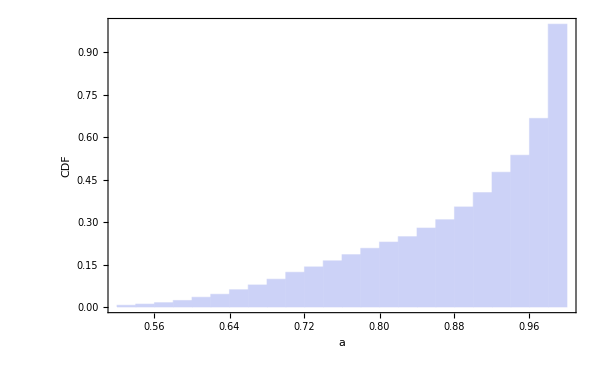

```mathematica
(*From Reynolds 2013*)
bhspins=({{"", 0.83, 0.13, 0.09}, {"", 0.84, 0, ∞}, {"", 0.92, 0.11, 0.03}, {"", 0.52, 0.15, 0.19}, {"", 0.66, 0.54, 0.30}, {"", 0.58, 0.74, 0.36}, {"", 0.89, 0, ∞}, {"", 0.64, 0.11, 0.19}, {"", 0.99, 0, ∞}, {"", 0.97, 0, ∞}, {"", 0.7, 0.1, 0.1}, {"", 0.89, 0, ∞}, {"", 0.88, 0, ∞}, {"", 0.99, 0, ∞}, {"", 0.97, 0, ∞}, {"", 0.987, 0, ∞}, {"", 0.98, 0, ∞}, {"", 0.52, 0, ∞}, {"", 0.6, 0.2, 0.2}, {"", 0.96, 0.11, 0.01}});
drawbhspin:=Module[{bhi=RandomInteger[{1,Length@bhspins}],side},side=RandomChoice[Flatten@Position[bhspins⟦2,{3,4}⟧,x_/;x≠0,{1},Heads->False]];var=bhspins⟦bhi,2+side⟧;bhspins⟦bhi,2⟧+Piecewise[{{RandomReal[](1-bhspins⟦bhi,2⟧),var==∞}},(2side-3) RandomVariate@TruncatedDistribution[{0,If[side==1,bhspins⟦bhi,2⟧,1-bhspins⟦bhi,2⟧]},HalfNormalDistribution[1/var]]]];
Show[Histogram[Table[drawbhspin,{10000}],Automatic,"CDF"],Frame->True,PlotRangePadding->0,FrameStyle->FontSize->20,ImageSize->600,FrameLabel->{"a","CDF"}]
```

```mathematica
eorb⟦7⟧
```

1.68188×10^17

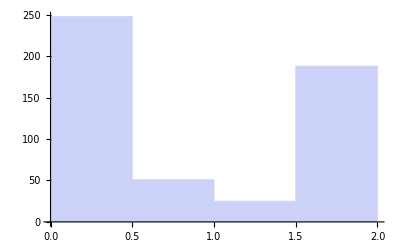

```mathematica
Histogram[2 Sin[Min[#,π/2]&/@(0.5collisioninfo⟦All,1,1⟧°)]^2]
```

```mathematica
FullSimplify[(1/2 v^2+1/2 v^2-(Norm[m{v,0}+m{v Cos[θ],v Sin[θ]}]/(2 m))^2),Assumptions->{θ>0,m>0,v>0}]
```

v^2 Sin[θ/2]^2

{{1.,2.,3.,4.,5.,5.5,6.,7.,7.5,8.,9.,10.},{5.95293293293293324,5.51051051051051033,5.26151151151151186,5.0981481481481481,4.88838838838838807,4.82142142142142127,4.79519519519519566,4.77087087087087092,4.76546546546546512,4.76216216216216193,4.76486486486486438,4.76775775775775745},{22.7297579647793953,24.4077740803256376,25.0831458989209928,25.4744213998214129,26.2168036219816685,26.6217475746572347,26.8218365318675645,27.0303444792260734,27.0648073445783695,27.1076309681521543,27.1298118087624438,27.1250698289126575}}

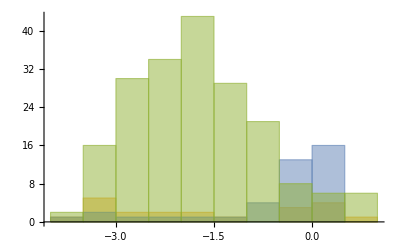

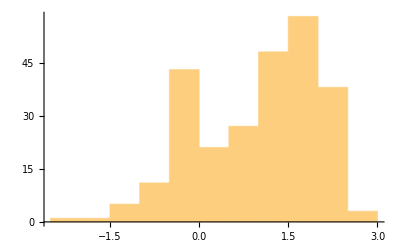

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Piecewise[{{-7.55511+0.936908 x, x<5.14042}, {-2.739+1.3629 (-5.14042+x), True}}]

-4.52066+0.613125 x

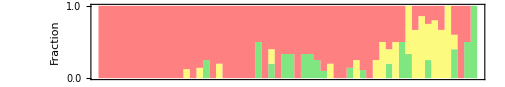
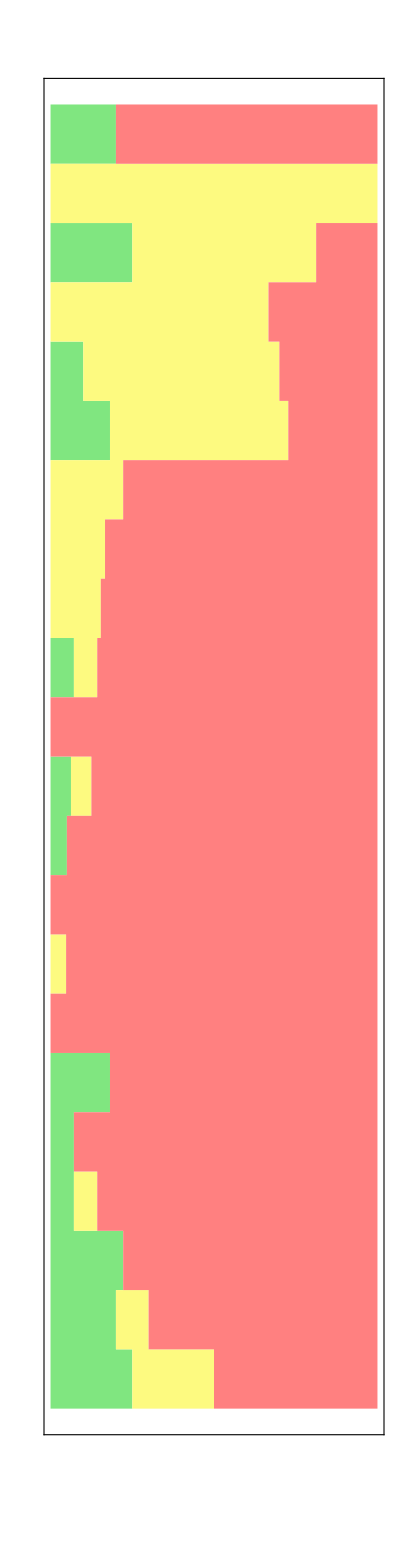
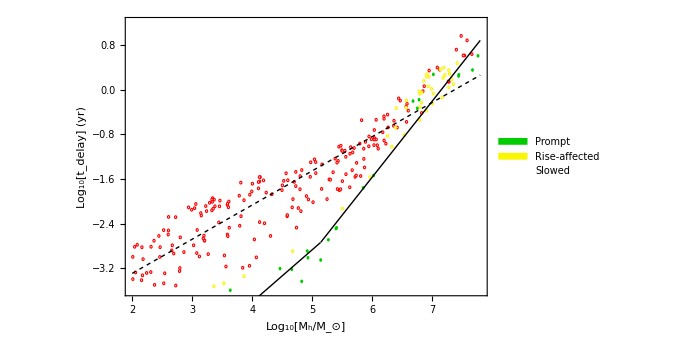
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Get[NotebookDirectory[]<>"CustomTicks.m"];
hexToRGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&;
αhr2=100;
tmb=2π √(((1/2 qs^(2/3)rss rsun/(Max[#,1]&/@βs))^3)/(G mhs msun));
typems[m_?NumericQ]:=If[m>0.3&&m<2,2,1];
tpeakco[type_?NumericQ,ββ_?NumericQ]:=Module[{β},If[type==1,
β=Min[2.5,Max[0.5,ββ]];(-0.30908+1.1804 √β-1.1764β)/(1+1.3089 √β-4.1940β),
β=Min[4,Max[0.6,ββ]];(-0.3867+0.57291 √β-0.31231β)/(1-1.2744 √β-0.90053β)]];
mpeakco[type_?NumericQ,ββ_?NumericQ]:=Module[{β},Exp[If[type==1,
β=Min[2.5,ββ];(10.253-17.380β+5.9988 β^2)/(1-0.46573β-4.5066 β^2),
β=Min[4,ββ];(27.261-27.516β+3.8716 β^2)/(1-3.2605β-1.3865 β^2)]]];
tpeakms[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=tpeakco[typems[ms],β] (mh/10^6)^(1/2)ms^-1 RMs[ms]^(3/2);
mpeakms[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=mpeakco[typems[ms],β](mh/10^6)^(-1/2)ms^2 RMs[ms]^(-3/2);
tpeakwd[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=tpeakco[If[ms>1,2,1],β] (mh/10^6)^(1/2)ms^-1 RWD[ms]^(3/2);
mpeakwd[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=mpeakco[If[ms>1,2,1],β](mh/10^6)^(-1/2)ms^2 RWD[ms]^(-3/2);
(*From Jamie's HWD sims*)
hwddat=Import[NotebookDirectory[]<>"log_tpeak_log_mdotpeak.dat"];
hwdtpeakf=Interpolation[{hwddat⟦1⟧,hwddat⟦2⟧}ᵀ];
hwdmpeakf=Interpolation[{hwddat⟦1⟧,hwddat⟦3⟧}ᵀ];
tpeakhwd[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=10^hwdtpeakf[Min[β,10]]/yr(mh/10^6)^(1/2);
mpeakhwd[β_?NumericQ,ms_?NumericQ,mh_?NumericQ]:=10^hwdmpeakf[Min[β,10]]yr/msun(mh/10^6)^(-1/2);

tpeak=Switch[startype,"WD",tpeakwd,"MS",tpeakms,"HWD",tpeakhwd];
mpeak=Switch[startype,"WD",mpeakwd,"MS",mpeakms,"HWD",mpeakhwd];
(*circtime=circorbs tmb/(((Min[#,0.9999]&)/@(1/(collisioninfo⟦All,1,2⟧ βs)))2 Sin[Min[#,π/2]&/@(0.5collisioninfo⟦All,1,1⟧°)]^2);*)

trimcollinfo=Table[collisioninfo⟦n,circcollind⟦n⟧⟧,{n,nexamples}];
eorb=(1/(trimcollinfo⟦All,2⟧ (*βs*)))2 Sin[Min[#,π/2]&/@(0.5Re@trimcollinfo⟦All,1⟧°)]^2 G mhs msun/(2 qs^(1/3)rss rsun/βs);
circtime=αhr2(*Sin[Min[#,π/2]&/@(0.5collisioninfo⟦All,1,1⟧°)]^-4*)π/(√2) G mhs msun eorb^(-3/2);
fillingtime=2π qs √(((rss/βs)/(Max[#,1]&/@βs))^3/(G mhs))(12^(1/3)qs^(1/9))/βs^(2/3);(*2π qs √(((rss/βs)/(Max[#,1]&/@βs))^3/(G mhs))qs^(1/3);*)
circtime=Min[#⟦1⟧,#⟦2⟧]&/@({circtime,fillingtime}ᵀ);
peaktime=((tpeak@@#)yr&)/@({βs,mss,mhs}ᵀ);
delaytime=tmb Max/@collidingstreams⟦All,1,1,{1,2}⟧(*+circtime*);
delaydat={Log10@mhs,Log10[delaytime/yr]}ᵀ;
circratio=circtime/peaktime;
(*circratio=circtime/(1/2 circorbs (1+circorbs)tmb);*)
spinlimit=0;
fastevents=Intersection[Position[circratio,x_/;x<1/3,{1},Heads->False],Position[aspins,x_/;x>spinlimit,{1},Heads->False]];
slowedevents=Intersection[Position[circratio,x_/;x>1,{1},Heads->False],Position[aspins,x_/;x>spinlimit,{1},Heads->False]];
affectedevents=Intersection[Position[circratio,x_/;1>x>1/3,{1},Heads->False],Position[aspins,x_/;x>spinlimit,{1},Heads->False]];
Histogram[Log10[{Extract[delaytime/yr,Complement[fastevents,affectedevents]],Extract[delaytime/yr,affectedevents],Extract[delaytime/yr,slowedevents]}]]
Histogram[Log10[circratio]]
delaycolors={hexToRGB@"#00CC00",hexToRGB@"#FAF500",Red};
delaycolorf=Piecewise[{{delaycolors⟦1⟧,#<1/3},{delaycolors⟦2⟧,1>#>1/3}},delaycolors⟦3⟧]&;
delaybinwidth=0.2;
delaybinspec={Floor[Log10[Min[delaytime]/yr],delaybinwidth],1.2(*Ceiling[Log10[Max[delaytime]/yr],delaybinwidth]*),delaybinwidth};

bcs=BinCounts[#,delaybinspec]&/@Log10[{Extract[delaytime,Complement[fastevents,affectedevents]],Extract[delaytime,affectedevents],Extract[delaytime,slowedevents]}/yr];
fracs=Transpose@Join[{Range[delaybinspec⟦1⟧,delaybinspec⟦2⟧-delaybinspec⟦3⟧,delaybinspec⟦3⟧]+delaybinspec⟦3⟧/2},{#},1]&/@Accumulate[N@#/Total[bcs,{1}]&/@bcs];
fracs=Join[fracs,{Join[{ConstantArray[delaybinspec⟦2⟧+delaybinspec⟦3⟧/2,Length@bcs]},{fracs⟦All,-1⟧⟦All,2⟧}]ᵀ}ᵀ,2];
sidehist=Show[Graphics[GeometricTransformation[ListPlot[fracs,InterpolationOrder->0,Joined->True,PlotStyle->None(*(Directive[#,AbsoluteThickness@1.5]&/@{Green,Yellow,Red})*),PlotRange->{All,{0,1}},Axes->False,PlotRangePadding->0,Filling->{{1->{Axis,Lighter[delaycolors⟦1⟧,0.5]}},{2->{{1},Lighter[delaycolors⟦2⟧,0.5]}},{3->{{2},Lighter[delaycolors⟦3⟧,0.5]}}},Background->None][[1,2]],ReflectionTransform[{-1,1}]]],Frame->True,FrameStyle->Directive[AbsoluteThickness@1,FontSize->20,Black,FontFamily->"Times"],AspectRatio->4,ImagePadding->{{15,15},{55,55}},PlotRangePadding->None,FrameTicks->{{None,None},{LinTicks[0,1,0.5,5,ShowTickLabels->False,MajorTickLength->{0.1,0},MinorTickLength->{0.05,0}],LinTicks[0,1,0.5,5,MajorTickLength->{0.1,0},MinorTickLength->{0.05,0}]}},ImageSize->{Automatic,405},Background->None,FrameLabel->{{None,None},{None,"Fraction"}}];

mhbinwidth=0.1;
mhbinspec={Floor[Log10[Min[mhs]],mhbinwidth],Ceiling[Log10[Max[mhs]],mhbinwidth],mhbinwidth};
bcs=BinCounts[#,mhbinspec]&/@Log10@{Extract[mhs,Complement[fastevents,affectedevents]],Extract[mhs,affectedevents],Extract[mhs,slowedevents]};
fracs=Transpose@Join[{Range[mhbinspec⟦1⟧,mhbinspec⟦2⟧-mhbinspec⟦3⟧,mhbinspec⟦3⟧]+mhbinspec⟦3⟧/2},{#},1]&/@Accumulate[N@#/Total[bcs,{1}]&/@bcs];
fracs=Join[fracs,{Join[{ConstantArray[mhbinspec⟦2⟧+mhbinspec⟦3⟧/2,Length@bcs]},{fracs⟦All,-1⟧⟦All,2⟧}]ᵀ}ᵀ,2];
tophist=ListPlot[fracs,InterpolationOrder->0,Joined->True,PlotStyle->None(*(Directive[#,AbsoluteThickness@1.5]&/@{Green,Yellow,Red})*),PlotRange->{All,{0,1}},Axes->False,Frame->True,PlotRangePadding->0,AspectRatio->1/5.75,Filling->{{1->{Axis,Lighter[delaycolors⟦1⟧,0.5]}},{2->{{1},Lighter[delaycolors⟦2⟧,0.5]}},{3->{{2},Lighter[delaycolors⟦3⟧,0.5]}}},ImageSize->{505,Automatic},ImagePadding->{{60,2},{10,10}},FrameStyle->Directive[AbsoluteThickness@1,FontSize->20,Black,FontFamily->"Times"],FrameTicks->{{LinTicks[0,1,0.5,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,1,0.5,5,ShowTickLabels->False,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}]},{None,None}},FrameLabel->{None,"Fraction"}];
fitfunc=Piecewise[{{aa x+bb,x<cc}},dd(x-cc)+aa cc+bb];
myfit=FindFit[Extract[delaydat,Complement[fastevents,affectedevents]],fitfunc,{{aa,1},bb,{cc,6},{dd,1}},x,MaxIterations->1000];
fit1=fitfunc/.myfit
fit2=Fit[Extract[delaydat,slowedevents],{1,x},x]

delayspl=Show[Graphics[{FaceForm@White}~Join~Riffle[Disk[#,Scaled[{0.003,0.003GoldenRatio}]]&/@(Extract[delaydat,slowedevents]),(EdgeForm@delaycolorf[#]&)/@Extract[circratio,slowedevents]]~Join~Riffle[Disk[#,Scaled[{0.003,0.003GoldenRatio}]]&/@(Extract[delaydat,affectedevents]),(EdgeForm@delaycolorf[#]&)/@Extract[circratio,affectedevents]]~Join~{EdgeForm[]}~Join~Riffle[Disk[#,Scaled[{0.004,0.004GoldenRatio}]]&/@(Extract[delaydat,fastevents]),delaycolorf/@Extract[circratio,fastevents]]],Plot[fit1,{x,mhbinspec⟦1⟧,mhbinspec⟦2⟧},PlotStyle->Directive[Black,AbsoluteThickness@1]],Plot[fit2,{x,mhbinspec⟦1⟧,mhbinspec⟦2⟧},PlotStyle->Directive[Black,AbsoluteThickness@1,AbsoluteDashing[{3,3}]]],Frame->True,AspectRatio->Full,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1,Black,FontFamily->"Times"],FrameLabel->{Row[{"Log_10[M_h/",DisplayForm@SubscriptBox["M","⊙"],"]"}],"Log_10[t_delay] (yr)"},PlotRange->{{mhbinspec⟦1⟧,mhbinspec⟦2⟧},{delaybinspec⟦1⟧,delaybinspec⟦2⟧}},ImageSize->{515,350},PlotRangeClipping->True,ImagePadding->{{60,12},{55,1}},Background->None,Epilog->Inset[Grid[{
{Graphics[{delaycolors⟦1⟧,Disk[]},ImageSize->12],Style["Prompt",FontSize->16,FontFamily->"Times"]},
{Graphics[{delaycolors⟦2⟧,Disk[]},ImageSize->12],Style["Rise-affected",FontSize->16,FontFamily->"Times"]},
{Graphics[{EdgeForm@delaycolors⟦3⟧,FaceForm@White,Disk[]},ImageSize->12],Style["Slowed",FontSize->16,FontFamily->"Times"]}
},Alignment->{Left,Top}],Scaled[{0.9,0.14}],Scaled[{1,0}]]];

delayscombpl=Grid[{{tophist, sidehist},{delayspl,SpanFromAbove}},Spacings->0,Alignment->{Left,Bottom},Background->White]
Export[NotebookDirectory[]<>"tdelay"<>fsuffix<>".pdf",delayscombpl];

delaypeakdat={Log10[peaktime/yr],Log10[delaytime/peaktime]}ᵀ;
```

```mathematica
cc/.myfit
```

7.02744

```mathematica
10^(-10.086770439851035+1.4364388931965324 x)/.x->7
```

0.929612

```mathematica
10^(0.007723713847680003+0.8202170075570758 (-7.027444189592543+x))/.x->7
```

0.966526

```mathematica
10^(-5.49442953602076+0.7798069082383062 x)/.x->7
```

0.920913

```mathematica
Length[Intersection[Position[circratio,x_/;x<1/3,{1},Heads->False],Position[aspins,x_/;x<0.2,{1},Heads->False]]]/Length[Position[aspins,x_/;x<0.2,{1},Heads->False]]//N
Length[Intersection[Position[circratio,x_/;x<1/3,{1},Heads->False],Position[aspins,x_/;x>0.8,{1},Heads->False]]]/Length[Position[aspins,x_/;x>0.8,{1},Heads->False]]//N
```

0.226986

0.280285

```mathematica
Length[Max/@Flatten[collidingstreams⟦All,All,1,{1,2}⟧,1]]
```

4797

```mathematica
Length@aspins
```

4096

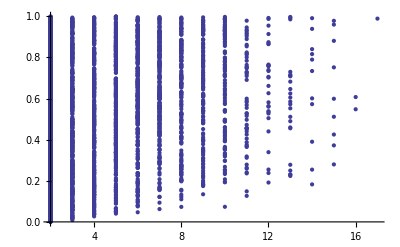

```mathematica
ListPlot[{Table[Max[collidingstreams⟦i,circcollind⟦i⟧,1,{1,2}⟧],{i,nexamples}],aspins}ᵀ,PlotRange->All]
```

```mathematica
Mean[Extract[Table[Max[collidingstreams⟦i,circcollind⟦i⟧,1,{1,2}⟧],{i,nexamples}],Position[aspins,x_/;x<0.1,{1},Heads->False]]]//N
```

2.40648

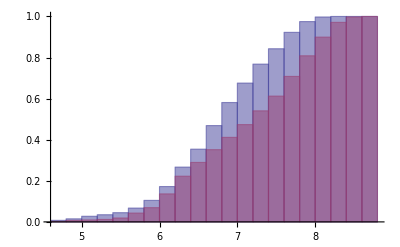

```mathematica
Histogram[{Extract[Log10@delaytime,Position[aspins,x_/;x<0.1,{1},Heads->False]],Extract[Log10@delaytime,Position[aspins,x_/;x>0.9,{1},Heads->False]]},Automatic,"CDF"]
```

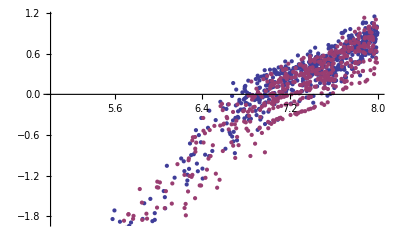

```mathematica
ListPlot[{Extract[delaydat,Intersection[fastspins,Complement[fastevents,affectedevents]]],Extract[delaydat,Intersection[slowspins,Complement[fastevents,affectedevents]]]}]
```

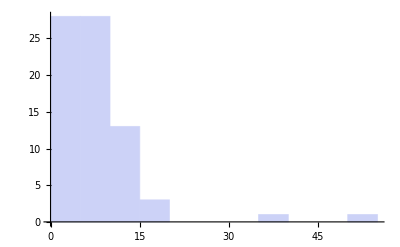

```mathematica
Histogram@Extract[βs,Intersection[Complement[fastevents,affectedevents],Position[Log10@mhs,x_/;x<6]]]
```

```mathematica
10^2 rsun/((2 G 10^6 msun)/c^2)
```

23.5443

```mathematica
(10^(-5.561526317263306+0.7840856611281847 x)/.x->Log10@m)/.m->10^7 m7
```

0.845422 m7^0.784086

```mathematica
10^(-11.808694780980469+1.7095847804882764 x)/.x->Log10[10^7 m7]
Simplify[10^(-0.22193594669352734+0.8348807860046201 (-6.784232595869049+x))/.x->Log10[10^7 m7]]
```

1.44012 m7^1.70958

0.908247 m7^0.834881

```mathematica
10^(Piecewise[{{-11.144008659997587+1.6099201433563115 x, x<6.784232595869049}, {-0.22193594669352734+0.8348807860046201 (-6.784232595869049+x), True}}])/.x->Log10[10^7 m7]
```

10^Piecewise[{{-11.144+0.699179 Log[10000000 m7], Log[10000000 m7]/Log[10]<6.78423}, {-0.221936+0.834881 (-6.78423+Log[10000000 m7]/Log[10]), True}}]

```mathematica
(Length@Select[Extract[colordata,slowedevents],#>0&])/(Length@slowedevents)//N
(Length@Select[Delete[colordata,slowedevents],#>0&])/(Length@Delete[colordata,slowedevents])//N
```

0.211708

0.237203

```mathematica
DeleteDirectory[nd<>"examples-fast",DeleteContents->True];
CreateDirectory[nd<>"examples-fast"];
Do[
CopyFile[nd<>"examples/example_"<>IntegerString[n,10,Length@IntegerDigits[nexamples]]<>".png",nd<>"examples-fast/example_"<>IntegerString[n,10,Length@IntegerDigits[nexamples]]<>".png"];
,{n,Flatten@Position[circratio,x_/;x<1/3]}]
DeleteDirectory[nd<>"examples-med",DeleteContents->True];
CreateDirectory[nd<>"examples-med"];
Do[
CopyFile[nd<>"examples/example_"<>IntegerString[n,10,Length@IntegerDigits[nexamples]]<>".png",nd<>"examples-med/example_"<>IntegerString[n,10,Length@IntegerDigits[nexamples]]<>".png"];
,{n,Flatten@Position[circratio,x_/;1>x>1/3]}]
DeleteDirectory[nd<>"examples-slow",DeleteContents->True];
CreateDirectory[nd<>"examples-slow"];
Do[
CopyFile[nd<>"examples/example_"<>IntegerString[n,10,Length@IntegerDigits[nexamples]]<>".png",nd<>"examples-slow/example_"<>IntegerString[n,10,Length@IntegerDigits[nexamples]]<>".png"];
,{n,Flatten@Position[circratio,x_/;x>1]}]
```

```mathematica
Length@Select[Extract[colordata,Position[Log10@mhs,x_/;5<x<6,{1},Heads->False]],#>0&]/Length@Extract[colordata,Position[Log10@mhs,x_/;5<x<6,{1},Heads->False]]//N
```

0.419516

```mathematica
tempo=Log10[(Max[#,1]&/@circratio)^-1(mpeakms@@#&/@({βs,mss,mhs}ᵀ))/medds];
```

```mathematica
Length@Select[Extract[tempo,Position[Log10@mhs,x_/;7<x<8,{1},Heads->False]],#>0&]/Length@Extract[tempo,Position[Log10@mhs,x_/;7<x<8,{1},Heads->False]]//N
```

0.0157776

```mathematica
With[{ms=0.3,mh=10^3,β=5},
Print[6RMs[ms]rsun/√((2 G mh msun β)/((mh/ms)^(1/3) RMs[ms]rsun))];
Print[(1/Max[3,β])^3 tpeak[β,ms,mh]yr];
Print[10(1/Max[3,β])^3 tpeak[β,ms,mh]yr];
]
```

61.257

823.934

8239.34

```mathematica
40 (10^3/10^6)^(1/2)86400//N
```

109288.

```mathematica
colllocs=Table[
collpoints=(sbsfs⟦n,1,#⟦1⟧⟧[#⟦2⟧]&/@({collidingstreams⟦n,All,1,1⟧,collidingstreams⟦n,All,2,2,1,2⟧}ᵀ))⟦All,;;3⟧;
collcoord=y/.collidingstreams⟦n,All,2,2⟧;
Position[collcoord,x_/;x==Min@collcoord]⟦1,1⟧
,{n,nexamples}];
```

```mathematica
collpairs=Table[collisioninfo⟦n,colllocs⟦n⟧,;;2⟧,{n,nexamples}];
```

```mathematica
Histogram3D[{Sin[collpairs⟦All,1⟧°/2]^2/collpairs⟦All,2⟧,Log10[βs collpairs⟦All,2⟧]}ᵀ,Automatic,{"Log","PDF"}]
```

-Graphics3D-

```mathematica
Histogram3D[{Sin[collpairs⟦All,1⟧°/2]^2,Log10[βs collpairs⟦All,2⟧]}ᵀ,Automatic]
```

-Graphics3D-

{-1.32039}

{1.,1.}

{-2.24367}

{0.979592,1.}

{-2.6989}

{0.571429,1.}

{-2.76498}

{0.38,0.66}

{-3.14692}

{0.0566038,0.0566038}

{-3.69076}

{0.,0.}

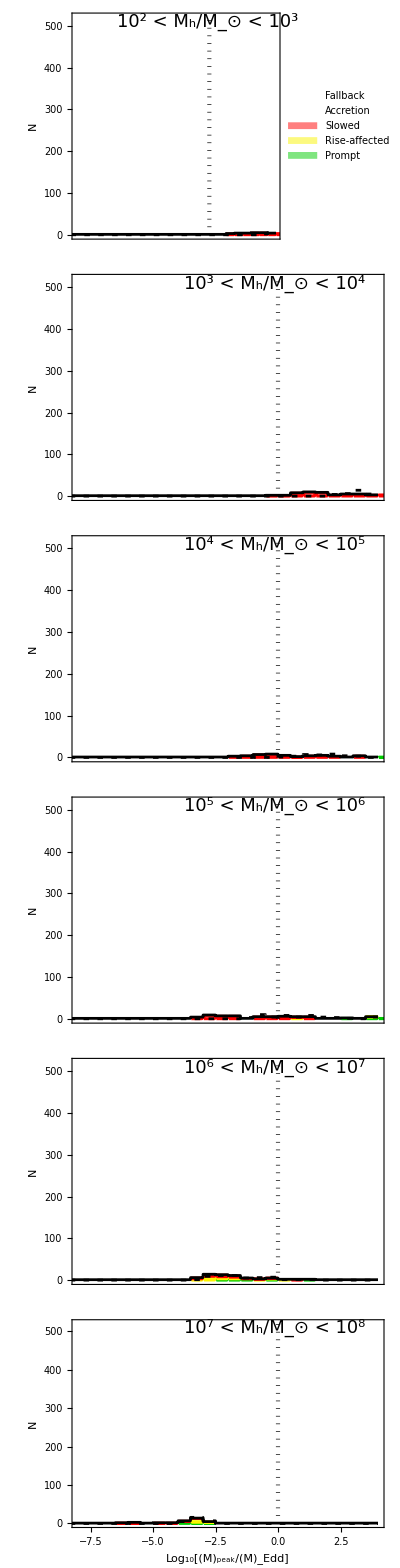
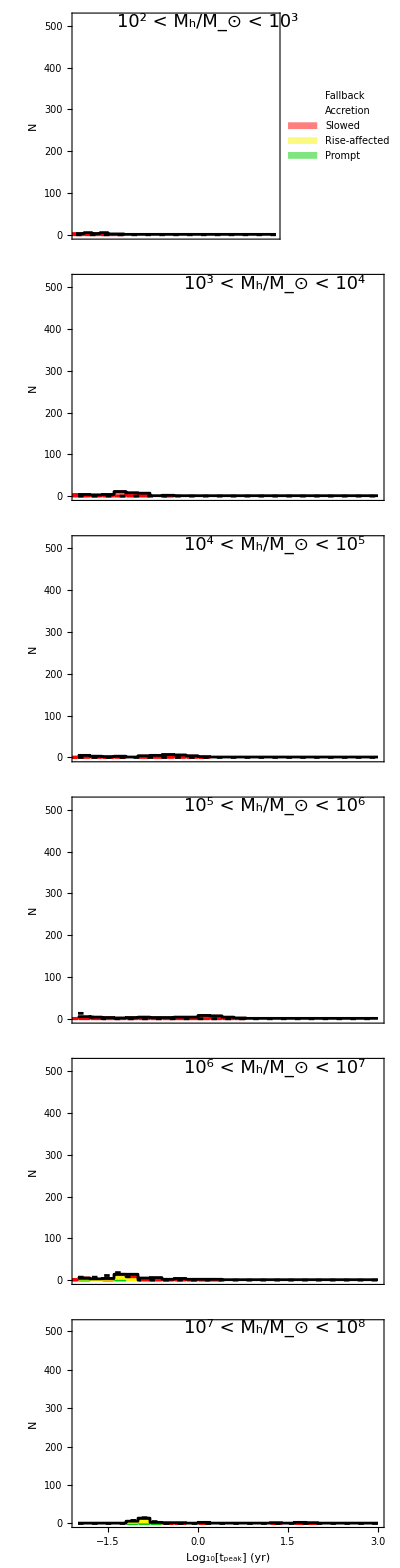

```mathematica
Get[NotebookDirectory[]<>"CustomTicks.m"];
z1=1+(1-a^2)^(1/3)((1+a)^(1/3)+((1-a)^(1/3)));
z2=√(3 a^2+z1^2);
risco=3+z2-√((3-z1)(3+z1+2z2));
ϵacc=1-√(1-2/(3 risco));
If[startype=="WD",
mue=2;
,
mue=1.18;
];
ymax=520;
ymajor=100;
medd[mh_?NumericQ,aa_?NumericQ]:=Block[{a=aa},1.257×10^38 mue/(ϵacc c^2)mh yr/msun];
ledd[mh_?NumericQ,aa_?NumericQ]:=Block[{a=aa},1.257×10^38 mue mh yr/msun];
medds=MapThread[medd,{mhs,aspins}];
mhbins=Range[lmhmin,lmhmax];
eddpl=ConstantArray[{},Length@mhbins-1];
Do[
mhcut=Position[Log10@mhs,x_/;mhbins⟦l⟧<x<mhbins⟦l+1⟧,{1},Heads->False];
colordata=Log10[(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))/medds];
colordataunsc=Extract[Log10[(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))/medds],mhcut];
colordatasc=Extract[Log10[(mpeak@@#&/@({βs,mss,mhs}ᵀ))/medds],mhcut];
Print[N@{Median@Extract[Log10[(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))],mhcut]}];
Print[N@{(Length@Select[colordataunsc,#>0&])/(Length@colordataunsc),(Length@Select[colordatasc,#>0&])/(Length@colordatasc)}];
f[{{xmin_,xmax_},{ymin_,ymax_}},___]:={(*EdgeForm@AbsoluteThickness@2,*)Rectangle[{xmin+0.035,If[ymin==0,ymin,ymin+1.99]},{xmax-0.035,ymax(*-0.99*)}]};
unschist=Plot[Evaluate[0.5(Length@colordatasc)PDF[HistogramDistribution[colordatasc,{0.5}],x]],{x,-10,4},Exclusions->None,PlotPoints->100,PlotStyle->Directive[Black,AbsoluteThickness@2,AbsoluteDashing@{4,6}],PlotRange->All];
schist=Plot[Evaluate[1+0.5(Length@colordataunsc)PDF[HistogramDistribution[colordataunsc,{0.5}],x]],{x,-10,4},Exclusions->None,PlotPoints->100,PlotStyle->Directive[Black,AbsoluteThickness@2],PlotRange->All];
theplot=Show[Histogram[{Extract[colordata,Intersection[mhcut,Complement[fastevents,affectedevents]]],Extract[colordata,Intersection[mhcut,affectedevents]],Extract[colordata,Intersection[mhcut,slowedevents]]},{0.5},FrameLabel->{If[l==Length@mhbins-1,"Log_10[(Ṁ)_peak/(Ṁ)_Edd]"],"N"},Frame->True,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1,Black,FontFamily->"Times"],ImageSize->{600,If[l==Length@mhbins-1,360,If[l==1,302,300]]},ChartElementFunction->f,ChartBaseStyle->AbsoluteThickness@0,ChartStyle->Table[Directive[EdgeForm@{AbsoluteThickness@2,delaycolors⟦i⟧,Opacity@1},FaceForm@delaycolors⟦i⟧],{i,3}],ChartLayout->"Stacked"],schist,unschist,ListPlot[{{0,0},{0,ymax}},Joined->True,PlotStyle->Directive[Black,AbsoluteThickness@3,CapForm@"Round",AbsoluteDashing@{0.001,5}]],PlotRange->{{-8,4},{0+If[l==Length@mhbins-1,0,0.01],ymax}},PlotRangePadding->0,PlotRangeClipping->True,AspectRatio->Full,FrameTicks->{{LinTicks[0,ymax,ymajor,5],LinTicks[0,ymax,ymajor,5,ShowTickLabels->False]},{If[l==Length@mhbins-1,Automatic,None],Automatic}},ImagePadding->{{60,10},{If[l==Length@mhbins-1,60,0],If[l==1,2,0]}},Epilog->Inset[Style[Row[{Superscript[10,mhbins⟦l⟧]," < M_h/",DisplayForm@SubscriptBox["M","⊙"]," < ",Superscript[10,mhbins⟦l+1⟧]}],FontSize->18,FontFamily->"Times",SingleLetterItalics->False],Scaled[{0.65,0.96}],Scaled[{1,1}]]];
eddpl⟦l⟧=If[l==1,Legended[theplot,Placed[SwatchLegend[Table[Graphics@{},{5}],{"Fallback","Accretion","Slowed","Rise-affected","Prompt"},LegendMarkerSize->{{18,18}},LegendMarkers->{Graphics[{EdgeForm@{Black,AbsoluteThickness@2,Opacity@1,AbsoluteDashing@{4,6}},FaceForm@White,Rectangle[]}],Graphics[{EdgeForm@{Black,AbsoluteThickness@2,Opacity@1},FaceForm@White,Rectangle[]}]}~Join~Reverse@Table[Graphics@{EdgeForm@{delaycolors⟦i⟧,AbsoluteThickness@2,Opacity@1},FaceForm@{delaycolors⟦i⟧,Opacity@0.5},Rectangle[]},{i,3}],LabelStyle->Directive[FontSize->16,FontFamily->"Times"]],{{0.04,0.95},{0,1}}]],theplot];
,{l,Length@mhbins-1}];

tpeakpl=ConstantArray[{},Length@mhbins-1];
Do[
mhcut=Position[Log10@mhs,x_/;mhbins⟦l⟧<x<mhbins⟦l+1⟧,{1},Heads->False];
colordata=Log10[(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)];
colordataunsc=Extract[Log10[(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)],mhcut];
colordatasc=Extract[Log10[(tpeak@@#&)/@({βs,mss,mhs}ᵀ)],mhcut];
f[{{xmin_,xmax_},{ymin_,ymax_}},___]:={(*EdgeForm@AbsoluteThickness@2,*)Rectangle[{xmin+0.01,If[ymin==0,ymin,ymin+1.99]},{xmax-0.01,ymax(*-0.99*)}]};
unschist=Plot[Evaluate[0.2(Length@colordatasc)PDF[HistogramDistribution[colordatasc,{0.2}],x]],{x,-2,3},Exclusions->None,PlotPoints->100,PlotStyle->Directive[Black,AbsoluteThickness@2,AbsoluteDashing@{4,6}],PlotRange->All];
schist=Plot[Evaluate[1+0.2(Length@colordataunsc)PDF[HistogramDistribution[colordataunsc,{0.2}],x]],{x,-2,3},Exclusions->None,PlotPoints->100,PlotStyle->Directive[Black,AbsoluteThickness@2],PlotRange->All];
theplot=Show[Histogram[{Extract[colordata,Intersection[mhcut,Complement[fastevents,affectedevents]]],Extract[colordata,Intersection[mhcut,affectedevents]],Extract[colordata,Intersection[mhcut,slowedevents]]},{0.2},FrameLabel->{If[l==Length@mhbins-1,"Log_10[t_peak] (yr)"],"N"},Frame->True,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1,Black,FontFamily->"Times"],ImageSize->{600,If[l==Length@mhbins-1,360,If[l==1,302,300]]},ChartElementFunction->f,ChartBaseStyle->AbsoluteThickness@0,ChartStyle->Table[Directive[EdgeForm@{AbsoluteThickness@2,delaycolors⟦i⟧,Opacity@1},FaceForm@delaycolors⟦i⟧],{i,3}],ChartLayout->"Stacked"],schist,unschist,PlotRange->{{-2,3},{0+If[l==Length@mhbins-1,0,0.01],ymax}},PlotRangePadding->0,PlotRangeClipping->True,AspectRatio->Full,FrameTicks->{{LinTicks[0,ymax,ymajor,5],LinTicks[0,ymax,ymajor,5,ShowTickLabels->False]},{If[l==Length@mhbins-1,Automatic,None],Automatic}},ImagePadding->{{60,10},{If[l==Length@mhbins-1,60,0],If[l==1,2,0]}},Epilog->Inset[Style[Row[{Superscript[10,mhbins⟦l⟧]," < M_h/",DisplayForm@SubscriptBox["M","⊙"]," < ",Superscript[10,mhbins⟦l+1⟧]}],FontSize->18,FontFamily->"Times",SingleLetterItalics->False],Scaled[{0.65,0.96}],Scaled[{1,1}]],Axes->False];
tpeakpl⟦l⟧=If[l==1,Legended[theplot,Placed[SwatchLegend[Table[Graphics@{},{5}],{"Fallback","Accretion","Slowed","Rise-affected","Prompt"},LegendMarkerSize->{{18,18}},LegendMarkers->{Graphics[{EdgeForm@{Black,AbsoluteThickness@2,Opacity@1,AbsoluteDashing@{4,6}},FaceForm@White,Rectangle[]}],Graphics[{EdgeForm@{Black,AbsoluteThickness@2,Opacity@1},FaceForm@White,Rectangle[]}]}~Join~Reverse@Table[Graphics@{EdgeForm@{delaycolors⟦i⟧,AbsoluteThickness@2,Opacity@1},FaceForm@{delaycolors⟦i⟧,Opacity@0.5},Rectangle[]},{i,3}],LabelStyle->Directive[FontSize->16,FontFamily->"Times"]],{{0.96,0.95},{1,1}}]],theplot];
,{l,Length@mhbins-1}];
mpeakcombpl=Column[eddpl,Center,0];
tpeakcombpl=Column[tpeakpl,Center,0];
Row[{mpeakcombpl,tpeakcombpl}]

Export[nd<>"mpeak"<>fsuffix<>".pdf",mpeakcombpl];
Export[nd<>"tpeak"<>fsuffix<>".pdf",tpeakcombpl];
```

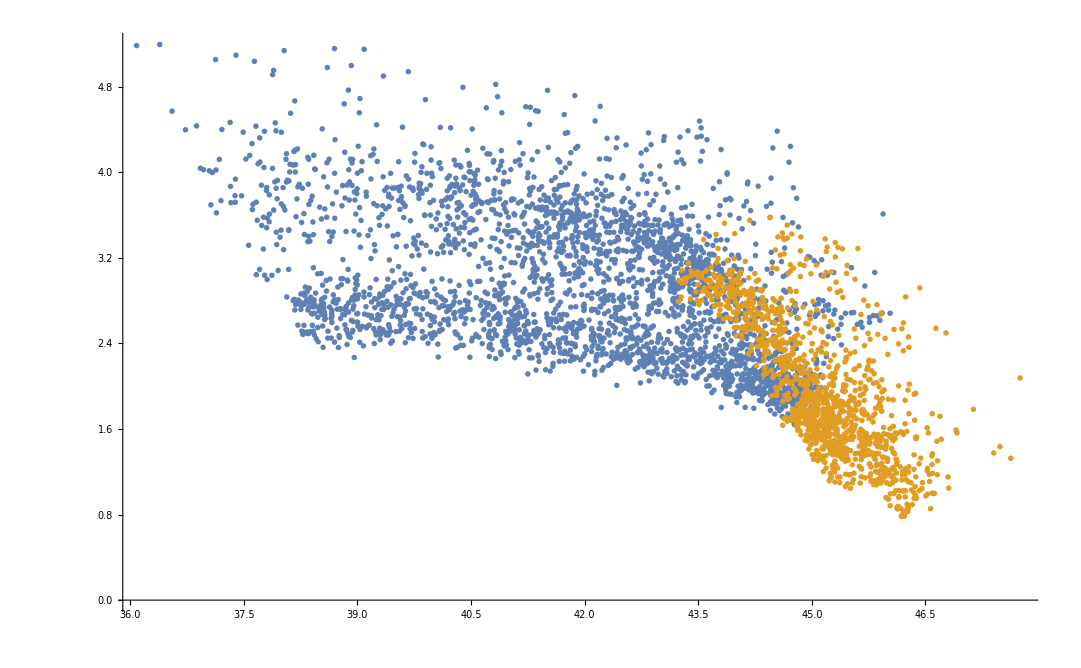

```mathematica
mpeaks=(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ));
subpos=Position[mpeaks/medds,x_/;x<1];
suppos=Position[mpeaks/medds,x_/;x≥1];
lpeaks=Log10[(ϵacc/.a->aspins)c^2 mpeaks msun/yr];
tpeaks=Log10[(Max[#,1]&/@circratio)((tpeak@@#&)/@({βs,mss,mhs}ᵀ))yr/day];
lpeakssub=Extract[lpeaks,subpos];
tpeakssub=Extract[tpeaks,subpos];
subweights=((10^lpeakssub rsun)/((8 G Extract[mhs,subpos]((tpeakssub day)/π)^2)^(2/3)))^(3/4);
subweights/=Max@subweights;
lpeakssup=Extract[lpeaks,suppos];
tpeakssup=Extract[tpeaks,suppos];
supweights=(10^lpeakssup)^(3/2);
supweights/=Max@supweights;
ListPlot[{{lpeakssub,tpeakssub}ᵀ,{lpeakssup,tpeakssup}ᵀ}]
```

```mathematica
Table[1-2.Erfc[s],{s,5}]
```

{0.685402,0.990645,0.999956,1.,1.}

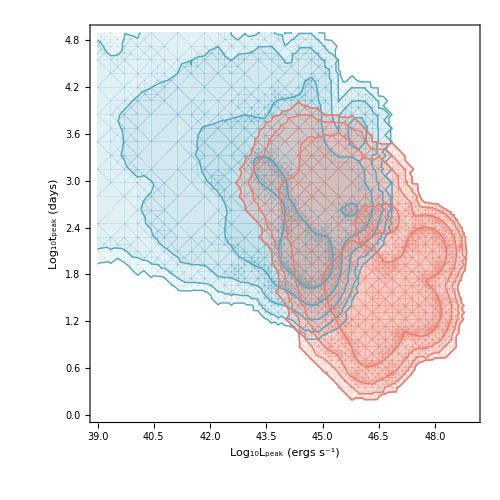
-Graphics- | -Graphics-
-Graphics- |

```mathematica
ci=24;cd1=5;cd2=1;
cd=ColorData[ci,"ColorList"];
nconts=5;

ranges={{39,49},{0,4.9}};

subcolor=cd⟦cd1⟧;
wd=WeightedData[{lpeakssub,tpeakssub}ᵀ,subweights];
skd=KernelMixtureDistribution[wd,MaxMixtureKernels->All];
pskd=PDF[skd,{l,t}];
(*ranges=pskd⟦2,0,1⟧+0.5{{-1,1},{-1,1}};*)
accumarr=Sort[{subweights,subweights}ᵀ,#1⟦1⟧>#2⟦1⟧&];
accumarr⟦All,1⟧=Accumulate[accumarr⟦All,1⟧];
accumarr⟦All,1⟧/=Max[accumarr⟦All,1⟧];
conts=Table[accumarr⟦Nearest[accumarr⟦All,1⟧->Range@Length@subpos,1-2Erfc[s]]⟦1⟧,2⟧,{s,nconts}];
subargs={pskd,{l}~Join~ranges⟦1⟧,{t}~Join~ranges⟦2⟧,PlotRange->All,Contours->conts,Method->{"TransparentPolygonMesh"->True},ClippingStyle->{None,Directive[Opacity[0.5],cd⟦cd1⟧]}};
subfillpl=ContourPlot@@Join[subargs,{ContourStyle->None,ContourShading->Table[Directive[Opacity[0.5 i/(nconts+1)],cd⟦cd1⟧],{i,0,nconts+1}]}];
subcontspl=ContourPlot@@Join[subargs,{ContourStyle->cd⟦cd1⟧,ContourShading->None}];

supcolor=cd⟦cd2⟧;
wd=WeightedData[{lpeakssup,tpeakssup}ᵀ,supweights];
skd=KernelMixtureDistribution[wd,MaxMixtureKernels->All];
pskd=PDF[skd,{l,t}];
(*ranges=pskd⟦2,0,1⟧+0.5{{-1,1},{-1,1}};*)
accumarr=Sort[{supweights,supweights}ᵀ,#1⟦1⟧>#2⟦1⟧&];
accumarr⟦All,1⟧=Accumulate[accumarr⟦All,1⟧];
accumarr⟦All,1⟧/=Max[accumarr⟦All,1⟧];
conts=Table[accumarr⟦Nearest[accumarr⟦All,1⟧->Range@Length@suppos,1-2Erfc[s]]⟦1⟧,2⟧,{s,nconts}];
supargs={pskd,{l}~Join~ranges⟦1⟧,{t}~Join~ranges⟦2⟧,PlotRange->All,Contours->conts,Method->{"TransparentPolygonMesh"->True},ClippingStyle->{None,Directive[Opacity[0.5],cd⟦cd2⟧]}};
supfillpl=ContourPlot@@Join[supargs,{ContourStyle->None,ContourShading->Table[Directive[Opacity[0.5 i/(nconts+1)],cd⟦cd2⟧],{i,0,nconts+1}]}];
supcontspl=ContourPlot@@Join[supargs,{ContourStyle->cd⟦cd2⟧,ContourShading->None}];

hlsub=HistogramDistribution[WeightedData[lpeakssub,subweights],ranges⟦1⟧~Join~{0.5}];hlsup=HistogramDistribution[WeightedData[lpeakssup,supweights],ranges⟦1⟧~Join~{0.5}];
lhist=Show[DiscretePlot@@{{(Length@subpos)/nexamples PDF[hlsub,l],(Length@suppos)/nexamples PDF[hlsup,l]},{l}~Join~ranges⟦1⟧~Join~{0.01},PlotRange->All,PlotStyle->{cd⟦cd1⟧,cd⟦cd2⟧},AspectRatio->0.25,ImagePadding->{{50,5},{1,1}},Frame->True,Axes->False,FrameTicks->False},PlotRangePadding->{{0,0},{0,0.1}},ImageSize->{500,75},AspectRatio->Full];

htsub=HistogramDistribution[WeightedData[tpeakssub,subweights],ranges⟦2⟧~Join~{0.25}];htsup=HistogramDistribution[WeightedData[tpeakssup,supweights],ranges⟦2⟧~Join~{0.25}];
thist=Rotate[MapAt[Scale[#,{1,-1}]&,Show[DiscretePlot@@{{(Length@subpos)/nexamples PDF[htsub,l],(Length@suppos)/nexamples PDF[htsup,l]},{l}~Join~ranges⟦2⟧~Join~{0.01},PlotRange->All,PlotStyle->{cd⟦cd1⟧,cd⟦cd2⟧},AspectRatio->0.25,ImagePadding->{{50,1},{5,1}},Frame->True,Axes->False,FrameTicks->False},PlotRangePadding->{{0,0},{0.1,0}},ImageSize->{500,75},AspectRatio->Full],{1}],90°];

Grid[{{lhist,thist},{Show[subfillpl,supfillpl,subcontspl,supcontspl,PlotRange->ranges,FrameLabel->{"Log_10L_peak (ergs s^-1)","Log_10t_peak (days)"},FrameStyle->Directive[AbsoluteThickness@1,FontSize->16],ImageSize->{500,500},AspectRatio->Full,ImagePadding->{{50,5},{50,1}}],SpanFromAbove}},Spacings->0,Alignment->{Left,Bottom},Background->White]
```

```mathematica
hlsub=HistogramDistribution[WeightedData[lpeakssub,subweights],ranges⟦1⟧~Join~{0.5}];hlsup=HistogramDistribution[WeightedData[lpeakssup,supweights],ranges⟦1⟧~Join~{0.5}];
lhist=Show[DiscretePlot@@{{(Length@subpos)/nexamples PDF[hlsub,l],(Length@suppos)/nexamples PDF[hlsup,l]},{l}~Join~ranges⟦1⟧~Join~{0.01},PlotRange->All,PlotStyle->{cd⟦cd1⟧,cd⟦cd2⟧},AspectRatio->0.25,ImagePadding->{{50,10},{1,1}},Frame->True,Axes->False,FrameTicks->False},PlotRangePadding->{{0,0},{0,0.1}},ImageSize->500];

htsub=HistogramDistribution[WeightedData[tpeakssub,subweights],ranges⟦2⟧~Join~{0.25}];htsup=HistogramDistribution[WeightedData[tpeakssup,supweights],ranges⟦2⟧~Join~{0.25}];
thist=Rotate[MapAt[Scale[#,{1,-1}]&,Show[DiscretePlot@@{{(Length@subpos)/nexamples PDF[htsub,l],(Length@suppos)/nexamples PDF[htsup,l]},{l}~Join~ranges⟦2⟧~Join~{0.01},PlotRange->All,PlotStyle->{cd⟦cd1⟧,cd⟦cd2⟧},AspectRatio->0.25,ImagePadding->{{50,10},{1,1}},Frame->True,Axes->False,FrameTicks->False},PlotRangePadding->{{0,0},{0.1,0}},ImageSize->500],{1}],90°]
```

-Graphics-

```mathematica
αhr2s=10^Range[0,4,0.1];
abovepromptfracs=aboveaffectfracs=belowpromptfracs=belowaffectfracs=ConstantArray[0,Length@αhr2s];
Do[
αhr2=αhr2s⟦i⟧;
circtime=αhr2(*Sin[Min[#,π/2]&/@(0.5collisioninfo⟦All,1,1⟧°)]^-4*)π/(√2) G mhs msun eorb^(-3/2);
fillingtime=2π qs √(((rss/βs)/(Max[#,1]&/@βs))^3/(G mhs))(12^(1/3)qs^(1/9))/βs^(2/3);(*2π qs √(((rss/βs)/(Max[#,1]&/@βs))^3/(G mhs))qs^(1/3);*)
circtime=Min[#⟦1⟧,#⟦2⟧]&/@({circtime,fillingtime}ᵀ);
peaktime=((tpeak@@#)yr&)/@({βs,mss,mhs}ᵀ);
delaytime=tmb Max/@collidingstreams⟦All,1,1,{1,2}⟧(*+circtime*);
delaydat={Log10@mhs,Log10[delaytime/yr]}ᵀ;
circratio=circtime/peaktime;
(*circratio=circtime/(1/2 circorbs (1+circorbs)tmb);*)
spinlimit=0;
mhcut=10^(cc/.myfit);
fastevents=Intersection[Position[circratio,x_/;x<1/3,{1},Heads->False],Position[mhs,x_/;x>mhcut,{1},Heads->False]];
slowedevents=Intersection[Position[circratio,x_/;x>1,{1},Heads->False],Position[mhs,x_/;x>mhcut,{1},Heads->False]];
affectedevents=Intersection[Position[circratio,x_/;1>x>1/3,{1},Heads->False],Position[mhs,x_/;x>mhcut,{1},Heads->False]];
numer=Length@fastevents+Length@slowedevents+Length@affectedevents;
abovepromptfracs⟦i⟧=N@((Length@fastevents)/numer);
aboveaffectfracs⟦i⟧=N@((Length@affectedevents)/numer);
fastevents=Intersection[Position[circratio,x_/;x<1/3,{1},Heads->False],Position[mhs,x_/;x<mhcut,{1},Heads->False]];
slowedevents=Intersection[Position[circratio,x_/;x>1,{1},Heads->False],Position[mhs,x_/;x<mhcut,{1},Heads->False]];
affectedevents=Intersection[Position[circratio,x_/;1>x>1/3,{1},Heads->False],Position[mhs,x_/;x<mhcut,{1},Heads->False]];
numer=Length@fastevents+Length@slowedevents+Length@affectedevents;
belowpromptfracs⟦i⟧=N@((Length@fastevents)/numer);
belowaffectfracs⟦i⟧=N@((Length@affectedevents)/numer);
,{i,Length@αhr2s}];
```

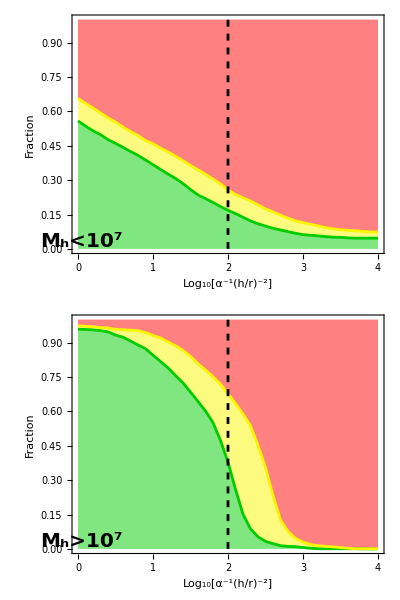

```mathematica
fiducialpl=ListPlot[{{2,0},{2,1}},Joined->True,PlotStyle->Directive[Black,AbsoluteThickness@2,AbsoluteDashing@5]];
viscouspl=Grid[{{Show[ListPlot[{{Log10[αhr2s],belowpromptfracs}ᵀ,{Log10[αhr2s],belowpromptfracs+belowaffectfracs}ᵀ},Joined->True,PlotStyle->(Directive[AbsoluteThickness@2,#]&/@delaycolors),Filling->{{1->{Bottom,Lighter[delaycolors⟦1⟧,0.5]}},{1->{{2},Lighter[delaycolors⟦2⟧,0.5]}},{2->{Top,Lighter[delaycolors⟦3⟧,0.5]}}},Frame->True,ImageSize->400,FrameLabel->{"Log_10[α^-1(h/r)^-2]","Fraction"},Axes->False,PlotRangePadding->0,FrameStyle->Directive[AbsoluteThickness@1,FontSize->16],PlotRange->{All,{0,1}},Epilog->{Inset[Style["M_h<10^7",Bold,FontSize->20,SingleLetterItalics->False],Scaled[{0.03,0.05}],Scaled[{0,0}]]}],fiducialpl]},
{Show[ListPlot[{{Log10[αhr2s],abovepromptfracs}ᵀ,{Log10[αhr2s],abovepromptfracs+aboveaffectfracs}ᵀ},Joined->True,PlotStyle->(Directive[AbsoluteThickness@2,#]&/@delaycolors),Filling->{{1->{Bottom,Lighter[delaycolors⟦1⟧,0.5]}},{1->{{2},Lighter[delaycolors⟦2⟧,0.5]}},{2->{Top,Lighter[delaycolors⟦3⟧,0.5]}}},Frame->True,ImageSize->400,FrameLabel->{"Log_10[α^-1(h/r)^-2]","Fraction"},Axes->False,PlotRangePadding->0,FrameStyle->Directive[AbsoluteThickness@1,FontSize->16],PlotRange->{All,{0,1}},Epilog->{Inset[Style["M_h>10^7",Bold,FontSize->20,SingleLetterItalics->False],Scaled[{0.03,0.05}],Scaled[{0,0}]]}],fiducialpl]
}}]
Export[nd<>"viscous.pdf",viscouspl];
```

```mathematica
Get[nd<>"msdat.mx"]
```

```mathematica
DumpSave[nd<>"msdat.mx",msdat];
```

```mathematica
msdat=Log10[{(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ),(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))/medds}ᵀ];
```

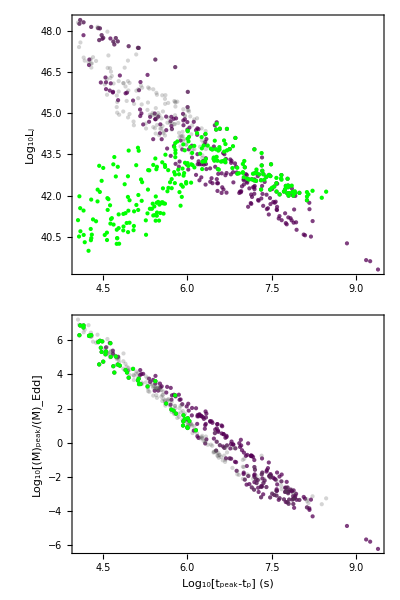

```mathematica
delayconst=1;
wdlpeakpl=ListPlot[{Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ],Log10[{yr(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ],
Log10[{yr(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2(Min[mpeak@@#⟦;;3⟧,medd[#⟦3⟧,#⟦4⟧]]&/@({βs,mss,mhs,aspins}ᵀ))}ᵀ](*,Extract[Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ],Position[βs,x_/;x>3]]*)},Axes->False,Frame->True,PlotRange->All,ImageSize->600,FrameStyle->Directive[Black,FontSize->20,AbsoluteThickness@1],FrameLabel->{{Style["Log_10L_j",SingleLetterItalics->False],"Log_10(Ṁ)_peak (M_⊙/yr)"},{Automatic,Automatic}},FrameTicks->{{Automatic,LinTicks[-5,6,2,4,TickPostTransformation->(#+Log10[msun/yr 0.1 c^2]&)]},{Automatic,Automatic}},PlotStyle->{Directive[Darker@Purple,Opacity@0.75],Directive[Darker@Gray,Opacity@0.25],Directive[PointSize@Medium,Green,Opacity@1]},ImagePadding->{{60,60},{0,10}},PlotTheme->"Classic"];
wdeddratpl=ListPlot[{Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))/(1medds)}ᵀ](*,msdat*),Log10[{yr(*(Max[#,1]&/@circratio)*)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,(*(Max[#,1]&/@circratio)^-1*)(mpeak@@#&/@({βs,mss,mhs}ᵀ))/(1medds)}ᵀ],Extract[Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))/(1medds)}ᵀ],Position[βs,x_/;x>3]]},Axes->False,Frame->True,PlotRange->All,ImageSize->600,FrameStyle->Directive[Black,FontSize->20,AbsoluteThickness@1],FrameLabel->{Row[{"Log_10[t_peak-",Subscript["t","p"],"] (s)"}],"Log_10[(Ṁ)_peak/(Ṁ)_Edd]"},PlotStyle->{Directive[Darker@Purple,Opacity@0.75],Directive[Darker@Gray,Opacity@0.25],Directive[PointSize@Medium,Green,Opacity@1]},ImagePadding->{{60,60},{60,0}},PlotTheme->"Classic"];
wdpl=Grid[{{wdlpeakpl},{wdeddratpl}},Spacings->{0,0}]
Export[nd<>"tpeak-lpeak-"<>fsuffix<>"eddrat.pdf",wdpl];
```

```mathematica
Length[(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))]
```

4096

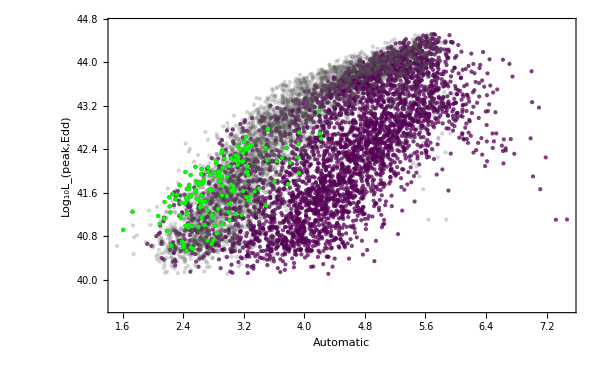

```mathematica
delayconst=1;
wdleddpeakpl=ListPlot[{Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2 Min[#]&/@({medds,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ)}ᵀ],Log10[{yr(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2 Min[#]&/@({medds,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ)}ᵀ],Extract[Log10[{yr(Max[#,1]&/@circratio)(tpeak@@#&)/@({βs,mss,mhs}ᵀ)+delayconst 10^delaydat⟦All,2⟧yr,msun/yr 0.1 c^2 Min[#]&/@({medds,(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))}ᵀ)}ᵀ],Position[βs,x_/;x>3]]},Axes->False,Frame->True,PlotRange->{All,{39.5,44.7}},ImageSize->600,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],FrameLabel->{{"Log_10L_(peak,Edd)","Log_10(Ṁ)_(peak,Edd) (M_⊙/yr)"},{Automatic,Automatic}},FrameTicks->{{Automatic,LinTicks[-7,6,1,4,TickPostTransformation->(#+Log10[msun/yr 0.1 c^2]&)]},{Automatic,Automatic}},PlotStyle->{Directive[Darker@Purple,Opacity@0.75],Directive[Darker@Gray,Opacity@0.25],Directive[PointSize@Medium,Green,Opacity@1]},ImagePadding->{{60,60},{0,5}}]
(*wdpl=Grid[{{wdlpeakpl},{wdeddratpl}},Spacings->{0,0}]
Export[nd<>"wd-tpeak-lpeak-eddrat-eddlim.pdf",wdpl];*)
```

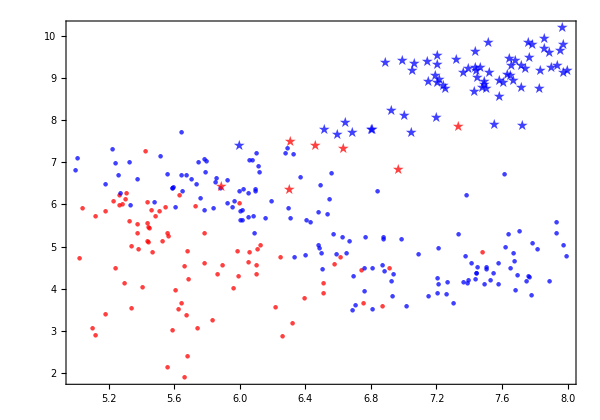

```mathematica
cyclets=ConstantArray[0,Length@collidingstreams];
Do[
Block[{orbs,θ,Ε,Μ,e},
orbs=collidingstreams⟦i,circcollind⟦i⟧,1⟧;
Do[
e=seccs⟦i,o-orbs⟦1⟧+1⟧;
cyclets⟦i⟧+=√((((qs⟦i⟧^(1/3)rss⟦i⟧rsun)/(βs⟦i⟧(1-e)))^3)/(G mhs⟦i⟧msun))If[o==orbs⟦1⟧||o==orbs⟦2⟧,
θ=2π If[o==orbs⟦1⟧,x,y]/.collidingstreams⟦i,circcollind⟦i⟧,2,2⟧;
Ε=Mod[2π+ArcTan[e+Cos[θ],√(1-e^2)Sin[θ]],2π];
Μ=Mod[2π+Ε-e Sin[Ε],2π];
If[o==orbs⟦1⟧,2π-Μ,Μ],2π 
];
,{o,orbs⟦1⟧,orbs⟦2⟧}];
]
,{i,Length@collidingstreams}]
eddrats=(Max[#,1]&/@circratio)^-1(mpeak@@#&/@({βs,mss,mhs}ᵀ))/medds;
ar=0.7;
j1644={Log10[7.4*10^6],Log10[5*10^4]};
cyclerats=cyclets/circtime;
cyclepl=Graphics[Join[Riffle[If[#>1,Red,Blue]&/@eddrats,If[#⟦3⟧>1,Text[Style["★",FontSize->14,Opacity@0.75],#⟦;;2⟧],Text[Style["●",FontSize->6,Opacity@0.75],#⟦;;2⟧]]&/@({Log10@mhs,Log10@cyclets,cyclerats}ᵀ)],{Black,Text[Style["★",FontSize->50],j1644],Yellow,Text[Style["★",FontSize->35],j1644]}],ImageSize->600,Frame->True,AspectRatio->ar,FrameStyle->Directive[Black,FontFamily->"Times",AbsoluteThickness@1,FontSize->18,SingleLetterItalics->False],FrameLabel->{Style["Log_10[M_h/M_⊙]",SingleLetterItalics->False],Style["Log_10t_cycle (s)",SingleLetterItalics->False]}]
Export[nd<>"tcycle"<>fsuffix<>".pdf",cyclepl];
```

```mathematica
Log10[1/(4.*10^-6)]
```

5.39794

```mathematica
1.3 √((2 G Mh msun)/(RMs[ms]rsun))(Mh/ms)^(1/6)/.{Mh->10^6,ms->1}
```

CompiledFunction::cfsa: Argument ms at position 1 should be a "machine-size real number".

8.03195×10^11 √((21.9408+0.00022582 Compile`$18)/(19.4142+0.0749017 Compile`$18))

```mathematica
Mean[Extract[Max[# msun/yr 0.1 c^2,0]&/@(mpeak@@#&/@({βs,mss,mhs}ᵀ)(Max[#,1]&/@circratio)^-1-medds)(Max[#,1]&/@circratio)((tpeak@@#&)/@({βs,mss,mhs}ᵀ))yr,Position[mhs,x_/;10^7<x<10^8]]]*10^-2/yr
Mean[Extract[medds msun/yr 0.1 c^2,Position[mhs,x_/;10^7<x<10^8]]]
Mean[Extract[(G mhs msun)/(qs^(2/3)rss rsun)(mss msun)/2,Position[mhs,x_/;x>10^7]]]
```

1.65522×10^42

6.66948×10^45

1.18817×10^51

```mathematica
Mean[Extract[(G mhs msun)/(qs^(2/3)rss rsun)(mss msun)/2,Position[mhs,x_/;x>10^7]]]*10^-2/yr
Mean[Extract[0.1mss msun c^2,Position[mhs,x_/;x>10^7]]]*10^-2/yr
```

3.76517×10^41

8.28837×10^43

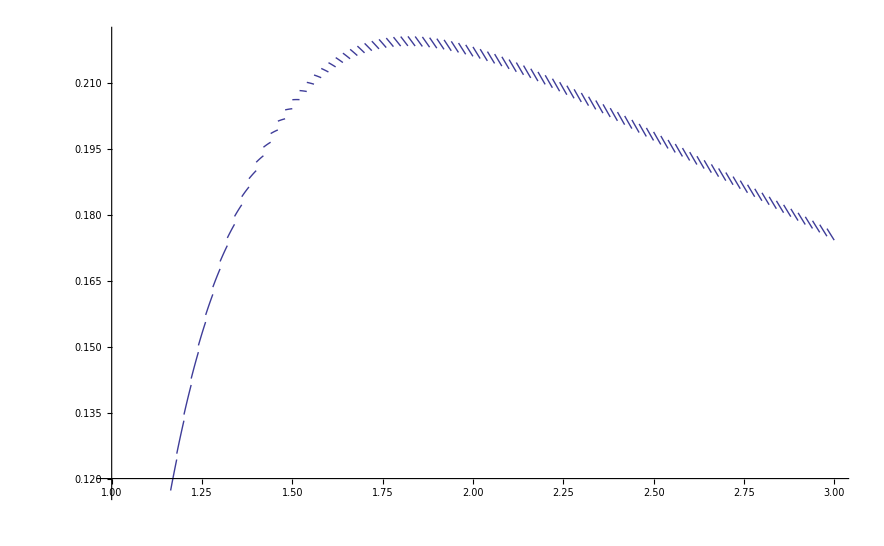

```mathematica
Plot[Log[x] x^(-5/3)((2+Mod[x,0.02])/2)^-1,{x,1,3},PlotPoints->200]
```

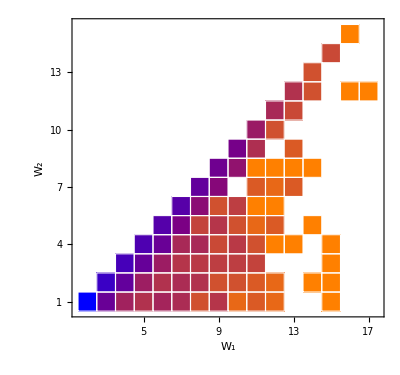
-Graphics- | -Graphics-

```mathematica
(*orbpairtally=Tally@Flatten[collidingstreams⟦All,All,1,{1,2}⟧,1];*)
orbpairtally=Tally@Table[collidingstreams⟦i,circcollind⟦i⟧,1,{1,2}⟧,{i,nexamples}];
maxtally=Max[orbpairtally⟦All,2⟧];
ticksspec=Table[{i,i,{0,0.02}},{i,20}];
lmaxtally=Log10@maxtally;
colorblend={Orange,Purple,Blue};
colorbar=Show[Graphics[Table[{Blend[colorblend,tally/lmaxtally],Rectangle[{0,tally},{1,tally+0.01}]},{tally,0,lmaxtally,0.01}]],AspectRatio->Full,ImageSize->{90,500},Frame->True,PlotRangePadding->0,FrameTicks->{{None,With[{x=Range[0,lmaxtally,0.5]},{x,NumberForm[#,{2,1}]&/@x}ᵀ]},{None,None}},FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],ImagePadding->{{5,55},{60,35}},FrameLabel->{{None,"Log_10N"},{None,None}}];
windingspl=Grid[{{Show[Graphics@Flatten[({Blend[colorblend,(Log10@#⟦2⟧)/(Log10@maxtally)],EdgeForm[White],Rectangle[Reverse@#⟦1⟧-{1/2,1/2}]}&/@orbpairtally)],Frame->True,PlotRangePadding->0,FrameTicks->{{ticksspec,ticksspec},{ticksspec,ticksspec}},FrameStyle->Directive[AbsoluteThickness@1,FontSize->20],ImagePadding->{{60,35},{60,35}},ImageSize->{Automatic,500},FrameLabel->{"W_1","W_2"}],colorbar}},Background->White]
Export[nd<>"windings"<>fsuffix<>".pdf",windingspl];
```

```mathematica
spindirs
```

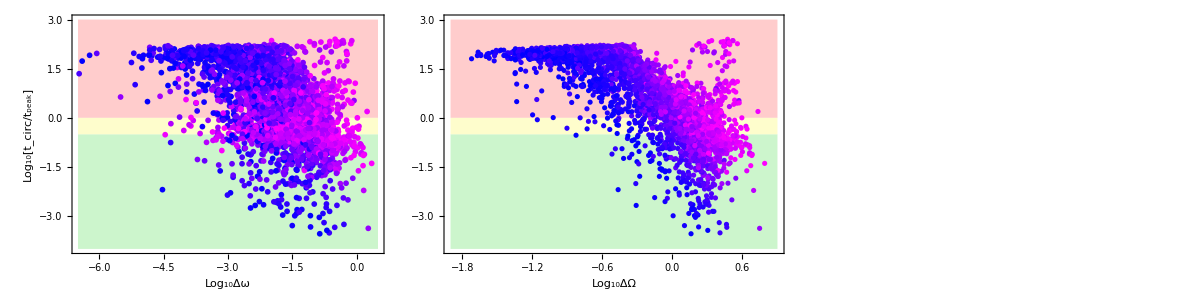

```mathematica
colorbar=Show[Graphics[Table[{Blend[{Blue,Magenta},(mh-5)/(8-5)],Rectangle[{0,mh},{1,mh+0.01}]},{mh,5,7.99,0.01}]],AspectRatio->Full,ImageSize->{90,400},Frame->True,PlotRangePadding->0,FrameTicks->{{None,With[{x=Range[5,8,0.5]},{x,NumberForm[#,{2,1}]&/@x}ᵀ]},{None,None}},FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],ImagePadding->{{10,55},{55,10}},FrameLabel->{{None,"Log_10M_h"},{None,None}}];
precpl=Grid[{{Show[ListPlot[{{{-6.5,-1/2},{0.5,-1/2}},{{-6.5,0},{0.5,0}}},PlotRange->{All,{-4,3}},Joined->True,Axes->False,Filling->{1->{Bottom,Lighter[delaycolors⟦1⟧,0.8]},2->{{1},Lighter[delaycolors⟦2⟧,0.8]},2->{Top,Lighter[delaycolors⟦3⟧,0.8]}},PlotStyle->None],Graphics[{PointSize[0.0075]}~Join~Riffle[(Blend[{Blue,Magenta},(#-5)/(8-5)]&)/@Log10@mhs,Point/@({Log10[(4π aspins)/(c^3 qs^(1/2))((βs G mhs msun)/(2 rss rsun))^(3/2)Abs[Dot[{0,0,1},#]&/@spindirs]],Log10@circratio}ᵀ)]],AspectRatio->Full,ImageSize->{550,400},Frame->True,PlotRangePadding->0,PlotRangeClipping->True,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],FrameLabel->{"Log_10Δω","Log_10[t_circ/t_peak]"},ImagePadding->{{55,1},{55,10}},PlotRange->All],Show[ListPlot[{{{-1.9,-1/2},{0.9,-1/2}},{{-1.9,0},{0.9,0}}},PlotRange->{All,{-4,3}},Joined->True,Axes->False,Filling->{1->{Bottom,Lighter[delaycolors⟦1⟧,0.8]},2->{{1},Lighter[delaycolors⟦2⟧,0.8]},2->{Top,Lighter[delaycolors⟦3⟧,0.8]}},PlotStyle->None],Graphics[{PointSize[0.0075]}~Join~Riffle[(Blend[{Blue,Magenta},(#-5)/(8-5)]&)/@Log10@mhs,Point/@({Log10[(6π G mhs msun βs)/(2 c^2 qs^(1/3)rss rsun)],Log10@circratio}ᵀ)]],AspectRatio->Full,ImageSize->{495,400},Frame->True,PlotRangePadding->0,PlotRangeClipping->True,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],FrameLabel->{"Log_10ΔΩ",None},ImagePadding->{{0,1},{55,10}}],colorbar}},Spacings->0]
Export[NotebookDirectory[]<>"circ-precession.pdf",precpl];
```

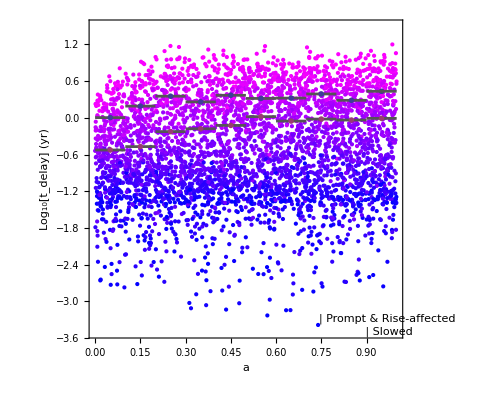
-Graphics- | -Graphics-

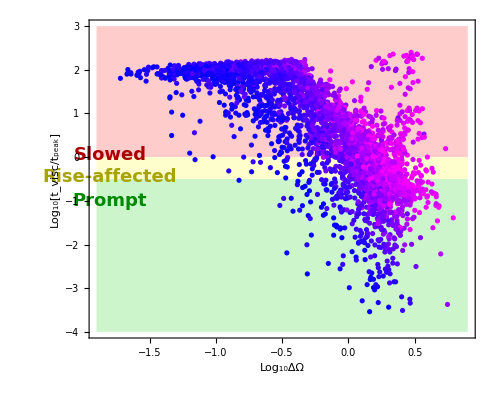
-Graphics- | -Graphics-

```mathematica
Needs["ErrorBarPlots`"];
selections={Union[fastevents,affectedevents],slowedevents}(*Complement[fastevents,affectedevents]*);
colordata=mhs;
mincolor=Min@Log10@colordata;
maxcolor=Max@Log10@colordata;
colorbar=Show[Graphics[Table[{Blend[{Blue,Magenta},(mh-Round@mincolor)/(Round@maxcolor-Round@mincolor)],Rectangle[{0,mh},{1,mh+0.01}]},{mh,5,7.99,0.01}]],AspectRatio->Full,ImageSize->{90,400},Frame->True,PlotRangePadding->0,FrameTicks->{{None,With[{x=Range[5,8,0.5]},{x,NumberForm[#,{2,1}]&/@x}ᵀ]},{None,None}},FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],ImagePadding->{{10,55},{55,10}},FrameLabel->{{None,"Log_10M_h"},{None,None}}];
ais=Range[0,1,0.1];
mediandat=Table[Table[{{(ais⟦i⟧+ais⟦i+1⟧)/2,Log10@Mean[Extract[10^delaydat,Intersection[Position[aspins,x_/;ais⟦i⟧<x<ais⟦i+1⟧],selections⟦j⟧]]⟦All,2⟧]},ErrorBar[(ais⟦2⟧-ais⟦1⟧)/2,0]},{i,Length@ais-1}],{j,Length@selections}];
medianpl=Show[ErrorListPlot[mediandat,PlotStyle->Directive[Darker@Gray,AbsoluteThickness@2]],
ListPlot[mediandat⟦All,All,1⟧,PlotMarkers->{{Graphics[{delaycolors⟦1⟧,Rotate[Rectangle[{0,-0.5},{1,0}],45°,{0,0}],delaycolors⟦2⟧,Rotate[Rectangle[{0,0},{1,0.5}],45°,{0,0}]}],0.065},{Graphics[{delaycolors⟦3⟧,Rotate[Rectangle[],45°]}],0.065}}]];
delaypl=Grid[{{Show[ListPlot[{{{0,-1/2},{0.9,-1/2}},{{0,0},{0.9,0}}},PlotRange->{All,{-3.5,1.5}},Joined->True,Axes->False,PlotStyle->None],Graphics[(*{PointSize[0.0075]}~Join~*)Flatten[{(Blend[{Blue,Magenta},(#-mincolor)/(maxcolor-mincolor)]&)/@(Log10@colordata),Point/@({aspins,Log10[delaytime/yr]}ᵀ)}ᵀ]],medianpl,AspectRatio->Full,ImageSize->{495,400},Frame->True,PlotRangePadding->0,PlotRangeClipping->True,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],FrameLabel->{"a","Log_10[t_delay] (yr)"},ImagePadding->{{70,12},{55,10}},Epilog->Inset[Framed[Grid[{
{Graphics[{delaycolors⟦1⟧,Rotate[Rectangle[{0,-0.5},{1,0}],45°,{0,0}],delaycolors⟦2⟧,Rotate[Rectangle[{0,0},{1,0.5}],45°,{0,0}]},ImageSize->20],Style["Prompt & Rise-affected",FontSize->16]},
{Graphics[{delaycolors⟦3⟧,Rotate[Rectangle[],45°]},ImageSize->20],Style["Slowed",FontSize->16]}
},Alignment->{Left,Center}],Background->Directive[White,Opacity@0.8],FrameStyle->None],Scaled[{0.95,0.04}],Scaled[{1,0}]]],colorbar}},Spacings->0]
viscpl=Grid[{{Show[ListPlot[{{{-1.9,-1/2},{0.9,-1/2}},{{-1.9,0},{0.9,0}}},PlotRange->{All,{-4,3}},Joined->True,Axes->False,Filling->{1->{Bottom,Lighter[delaycolors⟦1⟧,0.8]},2->{{1},Lighter[delaycolors⟦2⟧,0.8]},2->{Top,Lighter[delaycolors⟦3⟧,0.8]}},PlotStyle->None],Graphics[{PointSize[0.0075]}~Join~Riffle[(Blend[{Blue,Magenta},(#-5)/(8-5)]&)/@Log10@mhs,Point/@({Log10[(6π G mhs msun βs)/(2 c^2 qs^(1/3)rss rsun)],Log10@circratio}ᵀ)]],AspectRatio->Full,ImageSize->{495,400},Frame->True,PlotRangePadding->0,PlotRangeClipping->True,FrameStyle->Directive[FontSize->20,AbsoluteThickness@1],FrameLabel->{"Log_10ΔΩ","Log_10[t_visc/t_peak]"},ImagePadding->{{70,12},{55,10}},Epilog->{
Inset[Style["Prompt",Bold,FontSize->18,Darker@delaycolors⟦1⟧],{-1.8,-1},Scaled[{0,0}]],Inset[Style["Rise-affected",Bold,FontSize->18,Darker@delaycolors⟦2⟧],{-1.8,-0.46},Scaled[{0,0}]],
Inset[Style["Slowed",Bold,FontSize->18,Darker@delaycolors⟦3⟧],{-1.8,0.06},Scaled[{0,0}]]}],colorbar}},Spacings->0]
Export[NotebookDirectory[]<>"delay.pdf",delaypl];
Export[NotebookDirectory[]<>"visc.pdf",viscpl];
```

```mathematica
With[{i=1},Show[footpointpls⟦i,norbs⟦i⟧,1⟧,ImageSize->900]]
```

-Graphics-

```mathematica
ListAnimate[footpointpls⟦1,10,1⟧]
```

```mathematica
Grid[Partition[footpointpls⟦All,1,-1⟧,Min[Length@footpointpls,3]]]
```

-Graphics-

```mathematica
Do[frame=Grid[Partition[footpointpls⟦All,f⟧,Min[Length@footpointpls,3]]];
Export[NotebookDirectory[]<>"frames/frame_"<>IntegerString[f,10,Length@IntegerDigits[nellipses]]<>".png",frame];
,{f,nellipses}]
```

```mathematica
ReleaseHold[Hold[trimcollinfo⟦i,2⟧/βs⟦i⟧]/.i->52]
```

1.67875

```mathematica
exampleinds⟦3;;⟧
```

{52,26,13,430,2183,3478}

```mathematica
trimcollinfo⟦exampleinds⟦3;;⟧,2⟧βs⟦exampleinds⟦3;;⟧⟧
```

{11.9539,7.28189,18.0216,4.2746,6.30499,25.6544}

```mathematica
trimcollinfo⟦1⟧
```

{154.598,24.2363}

```mathematica
βs⟦exampleinds⟦3;;⟧⟧
```

{2.66847,0.892232,3.39842,0.500738,0.529236,0.538895}

```mathematica
padspace=20;
linet=2;
exampleinds={4059,4059,52,26,1,127,2183,3478};
filelist=(#⟦1⟧<>IntegerString[#⟦2⟧,10,Length@IntegerDigits[nexamples]]<>".png"&)/@({{"wide-","close-","fast-","med-","slow-","fast-","med-","slow-"},exampleinds}ᵀ);
images=ConstantArray[{},Length@filelist];
Do[images⟦f⟧=RemoveAlphaChannel@Show[Import[NotebookDirectory[]<>"examples-fig/"<>filelist⟦f⟧],ImageSize->If[f≤2,450,300],Epilog->Inset[Style[mhs⟦exampleinds⟦f⟧⟧,FontSize->16,Background->White,EdgeForm@Black]]],{f,Length@filelist}];
collageimg=ImageResize[ImageAssemble[Partition[ImagePad[#,padspace,White]&/@images⟦3;;⟧,3]],2000];
id=ImageDimensions@collageimg;
padsize=Round[(2000*padspace)/((1000+(2padspace))*3)];
topimg=ImageResize[ImagePad[ImageAssemble[images⟦;;2⟧],padsize,White],2000];
backgroundimg=ImageAssemble[{{topimg},{collageimg}}];
widemid=1000/(1000+padsize)1000/2+padsize;
zoomrad=1000/(1000+padsize)0.25;
angles=trimcollinfo⟦exampleinds⟦3;;⟧,1⟧;
dists=trimcollinfo⟦exampleinds⟦3;;⟧,2⟧;
exlabels={{"Prompt, delayed","Rise-affected, delayed","Slowed, delayed"},{"Prompt, no delay","Rise-affected, no delay","Slowed, no delay"}};
anglelabels=Partition[Table[Style["α_int = "<>ToString@NumberForm[angles⟦i⟧,{3,1}]<>"°\nr_int/r_t = "<>ToString@NumberForm[dists⟦i⟧,{3,1}],SingleLetterItalics->False,FontFamily->"Times"],{i,Length@angles}],3];
examplegridpl=Show[backgroundimg,Graphics[{FaceForm[],EdgeForm@{Black,AbsoluteThickness@1},Rectangle[{widemid-zoomrad,id⟦2⟧+widemid-zoomrad},{widemid+zoomrad,id⟦2⟧+widemid+zoomrad}],EdgeForm@{Black,AbsoluteThickness@linet},Rectangle[{1000+linet/2,id⟦2⟧+padsize+linet/2},{2000-linet/2-padsize,id⟦2⟧+1000-linet/2}],AbsoluteThickness@1,Line[{{widemid-zoomrad,id⟦2⟧+widemid-zoomrad},{1000+linet/2,id⟦2⟧+padsize+linet/2}}],Line[{{widemid-zoomrad,id⟦2⟧+widemid+zoomrad},{1000+linet/2,id⟦2⟧+1000-linet/2}}]}~Join~{EdgeForm@{Gray,AbsoluteThickness@linet}}
~Join~Flatten@Table[Rectangle[{2000/3(i-1)+padsize,id⟦2⟧/2(j-1)+padsize},{2000/3 i-padsize,id⟦2⟧/2j-padsize}],{i,3},{j,2}]
~Join~Flatten@Table[Style[Text[exlabels⟦j,i⟧,{2000/3 i-padsize-30,id⟦2⟧/2j-padsize-30},{1,1}],FontSize->20,Background->Directive[White,Opacity@0.75],FontFamily->"Times"],{i,3},{j,2}]
~Join~Flatten@Table[Style[Text[anglelabels⟦j,i⟧,{2000/3 i-padsize-30,id⟦2⟧/2(j-1)+padsize+120},{1,1}],FontSize->20,Background->Directive[White,Opacity@0.75],TextAlignment->Right,FontFamily->"Times"],{i,3},{j,2}]],ImageSize->800];
Show[examplegridpl,ImageSize->900]
Export[nd<>"examples.pdf",examplegridpl];
```

-Graphics-

```mathematica
bininfo=Import[nd<>"JamesOE.txt"(*"JamesbetahalfOE.txt"*),"Table"];
mdat=bininfo⟦All,{1,8}⟧*10^3;
adat=bininfo⟦All,{2,9}⟧*100;
edat=bininfo⟦All,{3,10}⟧;
idat=bininfo⟦All,{4,11}⟧;
ωdat=bininfo⟦All,{5,12}⟧;
Ωdat=bininfo⟦All,{6,13}⟧;

rpdat=(1-edat)adat;
rtdat=RMs[mdat/msun]rsun((10^6 msun)/mdat)^(1/3);
βdat=rtdat/rpdat;

(*Histogram[Log10@Flatten[βdat]]*)

Block[{i=60},
func=Composition[RotationTransform[-Mod[Ωdat⟦i,1⟧,π],{0,0,1}],RotationTransform[-Mod[idat⟦i,1⟧,π],{1,0,0}],RotationTransform[-Mod[ωdat⟦i,1⟧,π],{0,0,1}]][ellipsef2⟦;;3⟧]/.{e->1-((10^6 msun)/mdat⟦i,1⟧)^(-1/3)Max[βdat⟦i,1⟧,1],rp->rpdat⟦i,1⟧};
func2=Composition[RotationTransform[-Mod[Ωdat⟦i,2⟧,π],{0,0,1}],RotationTransform[-Mod[idat⟦i,2⟧,π],{1,0,0}],RotationTransform[-Mod[ωdat⟦i,2⟧,π],{0,0,1}]][ellipsef2⟦;;3⟧]/.{e->1-((10^6 msun)/mdat⟦i,2⟧)^(-1/3)Max[βdat⟦i,2⟧,1],rp->rpdat⟦i,2⟧};
Print[Show[{ParametricPlot3D[func,{θ,0,2π},PlotRange->All,ViewPoint->Top,PlotStyle->Red]/.Line[pts_,rest___]:>Tube[pts,(Norm/@pts)/(((10^6 msun)/mdat⟦i,1⟧)^(1/3)),rest],ParametricPlot3D[func2,{θ,0,2π},PlotRange->All,ViewPoint->Top,PlotStyle->Blue]/.Line[pts_,rest___]:>Tube[pts,(Norm/@pts)/(((10^6 msun)/mdat⟦i,2⟧)^(1/3)),rest]},Ticks->False]];
Print[Show[ParametricPlot3D[func,{θ,0,2π},PlotRange->All,ViewPoint->Top,PlotStyle->Directive[Red,Opacity@0.5]]/.Line[pts_,rest___]:>Tube[pts,(Norm/@pts)/(((10^6 msun)/mdat⟦i,1⟧)^(1/3)),rest],ParametricPlot3D[func2,{θ,0,2π},PlotRange->All,ViewPoint->Top,PlotStyle->Directive[Blue,Opacity@0.5]]/.Line[pts_,rest___]:>Tube[pts,(Norm/@pts)/(((10^6 msun)/mdat⟦i,2⟧)^(1/3)),rest],ViewPoint->Front,AspectRatio->1,Ticks->False]];
Print[Show[ParametricPlot3D[func,{θ,0,2π},PlotRange->All,PlotStyle->Directive[Red,Opacity@0.5]]/.Line[pts_,rest___]:>Tube[pts,(Norm/@pts)/(((10^6 msun)/mdat⟦i,1⟧)^(1/3)),rest],ParametricPlot3D[func2,{θ,0,2π},PlotRange->All,ViewPoint->Top,PlotStyle->Directive[Blue,Opacity@0.5]]/.Line[pts_,rest___]:>Tube[pts,(Norm/@pts)/(((10^6 msun)/mdat⟦i,2⟧)^(1/3)),rest],AspectRatio->1,Ticks->False,PlotRange->2Max[rpdat⟦i⟧]{{-1,1},{-1,1},{-0.1,0.1}},ViewPoint->Front]];
]
```

Part::take: Cannot take positions 1 through 3 in ellipsef2.

-Graphics3D-

-Graphics3D-

-Graphics3D-